```mathematica
1
```

1

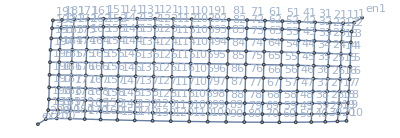

Switching costs simplified in 0.906491 seconds.

Balance equations solved in 11.3146 seconds.

TripleClean took 5.26146 seconds.

TripleClean again (with some more equalities) took 39.6141 seconds.

<|Vertices List→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,80,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200},51,1|>
 |  |  |  |

```mathematica
Data=DataG["Grid1020"];
d2e1=Data2Equations[Data];
d2e=MFGPreprocessing[d2e1]
```

```mathematica
(nn=CriticalCongestionSolver[d2e];)//AbsoluteTiming
```

MFGSS: Calculated the cost plus currents for the flow in 0.004821 seconds.

MFGS: Selecting inequalities by transition flow took 10.2549 seconds. 2056

MFGSS: Simplifying inequalities by transition flow took 45.6598 seconds.

{58.0086,Null}

```mathematica
rules=nn["AssoCritical"][[2]];
NewSystem=nn["AssoCritical"][[1]];
jts=nn["jts"];
{time,ineqsByTransition}=AbsoluteTiming[Select[NewSystem[[2]],Function[exp,!FreeQ[#][exp]]]&/@jts];
time
{time,altsByTransition}=AbsoluteTiming[Select[NewSystem[[3]],Function[exp,!FreeQ[#][exp]]]&/@jts];
time
```

42.1232

13.4899

```mathematica
order=OrderingBy[altsByTransition,Length];
```

```mathematica
Length/@altsByTransition[[order]];
Take[altsByTransition,100]
```

{True,True,True,True,True,True,1,1,True,True,True,True,1,1,True,True,True,True,1,1,True,True,True,True,1,1,True,True,True,43,True,True,1,1,1,1,1,1,1,True,True,True,True,True,1,1,1,1,1,1,1,True,True,True,True,True,1,1}
 |  |  |  |

```mathematica
Last/@%[[2]]
```

True

```mathematica
ineqsByTransition//Length
```

2056

```mathematica
And@@altsByTransition[[2000;;2010]]//Head
```

And

```mathematica
altsByTransition[[order]][[2000;;2001]]
```

```mathematica
mm1=2000;
mm=UpTo[mm1+20];
AbsoluteTiming[FinalStep[{{True,NewSystem[[2]],#},<||>}]&/@Take[altsByTransition[[order]],{mm1,mm}]//DeleteDuplicates]
```

Final: {0,9007,16}

Final: Iterative DNF convertion on 16 disjunctions took 18.4278 seconds to terminate.

```mathematica
mm1=2000;
mm=UpTo[mm1+20];
AbsoluteTiming[MapThread[FinalStep[{{True,#1,#2},<||>}]&,{Take[ineqsByTransition[[order]],{mm1,mm}],Take[altsByTransition[[order]],{mm1,mm}]}]//DeleteDuplicates]
```

Final: {0,55,16}

Final: Iterative DNF convertion on 16 disjunctions took 0.323515 seconds to terminate.

Final: Reducing (each alternative)... 128 of them.

Final: Reducing (each alternative), returned 4 of them, took 0.96458 seconds to terminate.

Now: 11:56:12GMT+3TimeObject[{11,56,12.14475},Instant,3.]The new rules are: <||>{0,0,168}

Final: {0,56,16}

Final: Iterative DNF convertion on 16 disjunctions took 0.330088 seconds to terminate.

Final: Reducing (each alternative)... 128 of them.

Final: Reducing (each alternative), returned 5 of them, took 1.01377 seconds to terminate.

Now: 11:56:15GMT+3TimeObject[{11,56,15.57743},Instant,3.]The new rules are: <||>{0,0,153}

Final: {0,56,16}

Final: Iterative DNF convertion on 16 disjunctions took 0.356878 seconds to terminate.

Final: Reducing (each alternative)... 128 of them.

Final: Reducing (each alternative), returned 5 of them, took 0.992072 seconds to terminate.

Now: 11:56:19GMT+3TimeObject[{11,56,19.720764},Instant,3.]The new rules are: <||>{0,0,153}

Final: {0,56,16}

Final: Iterative DNF convertion on 16 disjunctions took 0.371405 seconds to terminate.

Final: Reducing (each alternative)... 128 of them.

Final: Reducing (each alternative), returned 5 of them, took 0.967996 seconds to terminate.

Now: 11:56:24GMT+3TimeObject[{11,56,24.232182},Instant,3.]The new rules are: <||>{0,0,153}

Final: {0,56,16}

Final: Iterative DNF convertion on 16 disjunctions took 0.333429 seconds to terminate.

Final: Reducing (each alternative)... 128 of them.

Final: Reducing (each alternative), returned 5 of them, took 0.959875 seconds to terminate.

Now: 11:56:29GMT+3TimeObject[{11,56,29.003223},Instant,3.]The new rules are: <||>{0,0,153}

Final: {0,56,16}

Final: Iterative DNF convertion on 16 disjunctions took 0.36137 seconds to terminate.

Final: Reducing (each alternative)... 128 of them.

Final: Reducing (each alternative), returned 5 of them, took 0.965295 seconds to terminate.

Now: 11:56:33GMT+3TimeObject[{11,56,33.197563},Instant,3.]The new rules are: <||>{0,0,153}

Final: {0,56,16}

Final: Iterative DNF convertion on 16 disjunctions took 0.326925 seconds to terminate.

Final: Reducing (each alternative)... 128 of them.

Final: Reducing (each alternative), returned 5 of them, took 0.970643 seconds to terminate.

Now: 11:56:37GMT+3TimeObject[{11,56,37.493456},Instant,3.]The new rules are: <||>{0,0,153}

Final: {0,56,16}

Final: Iterative DNF convertion on 16 disjunctions took 0.411535 seconds to terminate.

Final: Reducing (each alternative)... 128 of them.

Final: Reducing (each alternative), returned 5 of them, took 1.09656 seconds to terminate.

Now: 11:56:42GMT+3TimeObject[{11,56,42.00961},Instant,3.]The new rules are: <||>{0,0,153}

Final: {0,52,16}

Final: Iterative DNF convertion on 16 disjunctions took 0.304225 seconds to terminate.

Final: Reducing (each alternative)... 128 of them.

Final: Reducing (each alternative), returned 4 of them, took 0.915703 seconds to terminate.

Now: 11:56:45GMT+3TimeObject[{11,56,45.660087},Instant,3.]The new rules are: <||>{0,0,152}

Final: {0,374,18}

Final: Iterative DNF convertion on 18 disjunctions took 5.94603 seconds to terminate.

Final: Reducing (each alternative)... 192 of them.

Final: Reducing (each alternative), returned 5 of them, took 2.26386 seconds to terminate.

Now: 11:56:54GMT+3TimeObject[{11,56,54.41065},Instant,3.]The new rules are: <||>{0,0,20}

Final: {0,265,18}

Final: Iterative DNF convertion on 18 disjunctions took 4.60547 seconds to terminate.

Final: Reducing (each alternative)... 192 of them.

Final: Reducing (each alternative), returned 3 of them, took 1.79074 seconds to terminate.

Now: 11:57:02GMT+3TimeObject[{11,57,2.336914},Instant,3.]The new rules are: <||>{0,0,36}

Final: {0,151,18}

Final: Iterative DNF convertion on 18 disjunctions took 1.76963 seconds to terminate.

Final: Reducing (each alternative)... 128 of them.

Final: Reducing (each alternative), returned 7 of them, took 2.1602 seconds to terminate.

Now: 11:57:06GMT+3TimeObject[{11,57,6.936003},Instant,3.]The new rules are: <||>{0,0,16}

Final: {0,92,18}

Final: Iterative DNF convertion on 18 disjunctions took 0.987575 seconds to terminate.

Final: Reducing (each alternative)... 128 of them.

Final: Reducing (each alternative), returned 5 of them, took 0.224053 seconds to terminate.

Now: 11:57:08GMT+3TimeObject[{11,57,8.375865},Instant,3.]The new rules are: <||>{0,0,10}

Final: {0,467,22}

Final: Iterative DNF convertion on 22 disjunctions took 27.0835 seconds to terminate.

Final: Reducing (each alternative)... 768 of them.

Final: Reducing (each alternative), returned 6 of them, took 10.9009 seconds to terminate.

Now: 11:57:47GMT+3TimeObject[{11,57,47.528433},Instant,3.]The new rules are: <||>{0,0,40}

Final: {0,366,22}

Final: Iterative DNF convertion on 22 disjunctions took 19.0521 seconds to terminate.

Final: Reducing (each alternative)... 768 of them.

Final: Reducing (each alternative), returned 3 of them, took 7.96559 seconds to terminate.

Now: 11:58:17GMT+3TimeObject[{11,58,17.877822},Instant,3.]The new rules are: <||>{0,0,72}

Final: {0,192,22}

Final: Iterative DNF convertion on 22 disjunctions took 7.70025 seconds to terminate.

Final: Reducing (each alternative)... 512 of them.

Final: Reducing (each alternative), returned 8 of them, took 6.48179 seconds to terminate.

Now: 11:58:33GMT+3TimeObject[{11,58,33.231923},Instant,3.]The new rules are: <||>{0,0,32}

Final: {0,125,22}

Final: Iterative DNF convertion on 22 disjunctions took 2.80534 seconds to terminate.

Final: Reducing (each alternative)... 512 of them.

Final: Reducing (each alternative), returned 6 of them, took 0.891585 seconds to terminate.

Now: 11:58:37GMT+3TimeObject[{11,58,37.257724},Instant,3.]The new rules are: <||>{0,0,20}

Final: {0,554,26}

Final: Iterative DNF convertion on 26 disjunctions took 126.445 seconds to terminate.

Final: Reducing (each alternative)... 3072 of them.

Final: Reducing (each alternative), returned 7 of them, took 48.7731 seconds to terminate.

Now: 12:01:34GMT+3TimeObject[{12,1,34.643863},Instant,3.]The new rules are: <||>{0,0,80}

Final: {0,461,26}

Final: Iterative DNF convertion on 26 disjunctions took 94.456 seconds to terminate.

Final: Reducing (each alternative)... 3072 of them.

Final: Reducing (each alternative), returned 7 of them, took 34.7369 seconds to terminate.

Now: 12:03:47GMT+3TimeObject[{12,3,47.89152},Instant,3.]The new rules are: <||>{0,0,144}

Final: {0,227,26}

Final: Iterative DNF convertion on 26 disjunctions took 32.2961 seconds to terminate.

Final: Reducing (each alternative)... 2048 of them.

Final: Reducing (each alternative), returned 9 of them, took 17.4408 seconds to terminate.

Now: 12:04:40GMT+3TimeObject[{12,4,40.086542},Instant,3.]The new rules are: <||>{0,0,64}

Final: {0,152,26}

Final: Iterative DNF convertion on 26 disjunctions took 8.66469 seconds to terminate.

Final: Reducing (each alternative)... 1536 of them.

Final: Reducing (each alternative), returned 7 of them, took 2.84159 seconds to terminate.

Now: 12:04:52GMT+3TimeObject[{12,4,52.137171},Instant,3.]The new rules are: <||>{0,0,24}

{525.131,{{{True,True,(j[169,179,189]≥0&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]+j[169,179,189]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159])||(355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159])||(j[169,179,189]≥0&&j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]+j[169,179,189]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159])||(j[169,179,189]≥0&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,180]+j[169,179,189]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159])||(j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,189]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,180]==0&&j[169,179,180]+j[169,179,189]+j[178,179,189]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,189])||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,180]==0&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,169]+j[178,179,189]+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[178,179,189]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190])||(j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726)||(j[169,179,180]+j[178,179,169]+j[178,179,180]≥3963633689369629503090930160342050/33486229776437911725602574322571&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170])||(355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]+j[169,179,189]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,169]+j[180,179,169]==0&&j[169,179,189]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]==16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]==3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169])||(j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[169,179,189]≥0&&j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,180]+j[169,179,189]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159])||(j[169,179,189]≥0&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]+j[169,179,189]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,169]+j[180,179,169]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]==3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169]&&200917378658627470353615445935426 j[178,179,189]<16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]≤16694856685371968418790170702189925/200917378658627470353615445935426)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,189]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[178,179,189]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[178,179,169]+j[180,179,169]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[169,179,180]+j[178,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,189]+j[178,179,169]+j[178,179,189]+j[179,180,170]+j[179,180,190]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]+j[179,180,170]+j[179,180,190]≤3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,180]==0&&j[169,179,180]+j[169,179,189]+j[178,179,189]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,189])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,169]+j[178,179,189]+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[178,179,189]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[178,179,180]==0&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,189]&&j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[178,179,180]==0&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,169]+j[178,179,189]+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[178,179,189]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726&&j[169,179,178]+j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[169,179,180]+j[178,179,169]+j[178,179,180]≥3963633689369629503090930160342050/33486229776437911725602574322571&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[169,179,180]+j[178,179,169]+j[178,179,180]≥3963633689369629503090930160342050/33486229776437911725602574322571&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]+j[169,179,189]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,169]+j[180,179,169]==0&&j[169,179,189]==0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]==16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]==3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[169,179,189]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142)||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142)||(j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,169]+j[180,179,169]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[169,179,180]+j[178,179,180]==j[179,180,170]+j[179,180,190]&&j[178,179,189]==0&&j[169,179,189]+j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,169]+j[178,179,180]&&j[179,180,170]+j[179,180,190]≤15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169])||(j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[179,180,170]+j[179,180,190]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,189]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,169]+j[180,179,169]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199])||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,169]+j[180,179,169]==0&&j[169,179,189]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]==16694856685371968418790170702189925&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,180]==0&&j[169,179,180]+j[169,179,189]+j[178,179,189]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,189])||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,180]==0&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,169]+j[178,179,189]+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[178,179,189]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190])||(j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726)||(j[169,179,180]+j[178,179,169]+j[178,179,180]≥3963633689369629503090930160342050/33486229776437911725602574322571&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170])||(355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170])||(355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[169,179,180]+j[169,179,189]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,169]+j[180,179,169]==0&&j[169,179,189]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]==16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]==3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169])||(j[169,179,189]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[169,179,189]≥0&&j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]+j[169,179,189]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]==3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169]&&200917378658627470353615445935426 j[178,179,189]<16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]≤16694856685371968418790170702189925/200917378658627470353615445935426)||(j[169,179,189]≥0&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,169]+j[180,179,169]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199])||(j[169,179,189]≥0&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,169]+j[180,179,169]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]<16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]≤16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[169,179,189]≥0&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[169,179,180]+j[169,179,189]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,169]+j[180,179,169]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]==3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169]&&200917378658627470353615445935426 j[178,179,189]<16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]≤16694856685371968418790170702189925/200917378658627470353615445935426)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[169,179,180]+j[178,179,180]==j[179,180,170]+j[179,180,190]&&j[178,179,189]==0&&j[169,179,189]+j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,169]+j[178,179,180]&&j[179,180,170]+j[179,180,190]≤15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[169,179,180]+j[178,179,180]==j[179,180,170]+j[179,180,190]&&j[178,179,189]==0&&j[169,179,189]+j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,169]+j[178,179,180]&&j[179,180,170]+j[179,180,190]≤15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[179,180,170]+j[179,180,190]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[179,180,170]+j[179,180,190]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[168,169,170]==0&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,189]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[178,179,169]+j[180,179,169]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,169]+j[180,179,169]==0&&j[169,179,189]==0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]==16694856685371968418790170702189925&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[169,179,180]+j[169,179,189]+j[178,179,189]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,189])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[169,179,189]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]==16694856685371968418790170702189925&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,169]+j[178,179,189]+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[178,179,189]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[169,179,180]+j[178,179,169]+j[178,179,180]≥3963633689369629503090930160342050/33486229776437911725602574322571&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[169,179,180]+j[169,179,189]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,169]+j[180,179,169]==0&&j[169,179,189]==0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]==16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]==3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[169,179,189]==0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[168,169,170]==0&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426)||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]+j[178,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,189]+j[178,179,169]+j[178,179,189]+j[179,180,170]+j[179,180,190]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]+j[179,180,170]+j[179,180,190]≤3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169])||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,180]==0&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,189]&&j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190])||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,180]==0&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,169]+j[178,179,189]+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[178,179,189]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190])||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726&&j[169,179,178]+j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[169,179,180]+j[178,179,169]+j[178,179,180]≥3963633689369629503090930160342050/33486229776437911725602574322571&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[169,179,189]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[169,179,180]+j[178,179,180]==j[179,180,170]+j[179,180,190]&&j[178,179,189]==0&&j[169,179,189]+j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,169]+j[178,179,180]&&j[179,180,170]+j[179,180,190]≤15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169])||(j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[179,180,170]+j[179,180,190]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,189]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[178,179,169]+j[180,179,169]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199])||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[169,179,180]+j[178,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,189]+j[178,179,169]+j[178,179,189]+j[179,180,170]+j[179,180,190]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]+j[179,180,170]+j[179,180,190]≤3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169])||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,180]==0&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,189]&&j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190])||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[169,179,189]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]==16694856685371968418790170702189925&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,180]==0&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,169]+j[178,179,189]+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[178,179,189]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190])||(j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726&&j[169,179,178]+j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,179,180]+j[178,179,169]+j[178,179,180]≥3963633689369629503090930160342050/33486229776437911725602574322571&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,170]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159])||(j[169,179,189]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[169,179,189]≥0&&j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199])||(j[169,179,189]≥0&&j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199])||(j[169,179,189]≥0&&j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169]&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]<16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]≤16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[169,179,189]≥0&&j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]<16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]≤16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[169,179,189]≥0&&j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[169,179,180]+j[169,179,189]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]==3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169]&&200917378658627470353615445935426 j[178,179,189]<16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]≤16694856685371968418790170702189925/200917378658627470353615445935426)||(j[169,179,189]≥0&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199])||(j[169,179,189]≥0&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]<16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]≤16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[169,179,180]+j[178,179,180]==j[179,180,170]+j[179,180,190]&&j[178,179,189]==0&&j[169,179,189]+j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,169]+j[178,179,180]&&j[179,180,170]+j[179,180,190]≤15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]==0&&j[168,169,170]==0&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[179,180,170]+j[179,180,190]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[169,179,189]==0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]==16694856685371968418790170702189925&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[159,169,179]+j[168,169,179]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]==j[168,169,159]+j[168,169,170]+j[168,169,179]&&j[159,169,170]+j[168,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]==0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159])||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159])||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]+j[178,179,180]==j[179,180,170]+j[179,180,190]&&j[178,179,189]==0&&j[169,179,189]+j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,169]+j[178,179,180]&&j[179,180,170]+j[179,180,190]≤15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169])||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]==0&&j[168,169,170]==0&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[179,180,170]+j[179,180,190]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[169,179,189]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]==16694856685371968418790170702189925&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[169,179,180]+j[178,179,180]==j[179,180,170]+j[179,180,190]&&j[178,179,189]==0&&j[169,179,189]+j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,169]+j[178,179,180]&&j[179,180,170]+j[179,180,190]≤15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169])||(j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]==0&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[179,180,170]+j[179,180,190]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[178,179,169]+j[180,179,169]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[169,179,180]+j[178,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,189]+j[178,179,169]+j[178,179,189]+j[179,180,170]+j[179,180,190]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]+j[179,180,170]+j[179,180,190]≤3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169])||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,170]==0&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,189]&&j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190])||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[169,179,189]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]==16694856685371968418790170702189925&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,169]+j[178,179,189]+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[178,179,189]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190])||(j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726&&j[169,179,178]+j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,179,180]+j[178,179,169]+j[178,179,180]≥3963633689369629503090930160342050/33486229776437911725602574322571&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[169,179,189]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[169,179,189]≥0&&j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199])||(j[169,179,189]≥0&&j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]<16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]≤16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[169,179,189]≥0&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199])||(j[169,179,189]≥0&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]<16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]≤16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[169,179,189]≥0&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199])||(j[169,179,189]≥0&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]<16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]≤16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[169,179,189]==0&&j[169,179,180]+j[178,179,169]+j[178,179,180]+j[178,179,189]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[168,169,170]==0&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,189]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426)||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&355329896791321240736340669025/7815668053784084893360386118+j[169,179,178]==j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[169,179,180]+j[178,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,189]+j[178,179,169]+j[178,179,189]+j[179,180,170]+j[179,180,190]==3963633689369629503090930160342050/33486229776437911725602574322571&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]+j[179,180,170]+j[179,180,190]≤3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169])||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]+j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,189]&&j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190])||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[178,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[179,180,170]+j[179,180,190]==j[178,179,169]+j[178,179,189]+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[178,179,189]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190])||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726&&j[169,179,178]+j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[169,179,180]+j[178,179,169]+j[178,179,180]≥3963633689369629503090930160342050/33486229776437911725602574322571&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[169,179,189]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[159,169,168]+j[159,169,170]+j[159,169,179]==964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[169,179,180]+j[178,179,180]==j[179,180,170]+j[179,180,190]&&j[178,179,189]==0&&j[169,179,189]+j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,169]+j[178,179,180]&&j[179,180,170]+j[179,180,190]≤15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169])||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[178,179,169]+j[180,179,169]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[169,179,189]==0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]==16694856685371968418790170702189925&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,170]+j[159,169,179]+j[168,169,170]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]==18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&511953655021311518296664481358775/18265216241693406395783222357766+j[159,169,168]≤j[168,169,159]+j[168,169,170]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[169,170,160]+j[169,170,180]==1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]==4882445493134427294312157127808875&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[170,169,159]&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[169,179,180]+j[178,179,180]==j[179,180,170]+j[179,180,190]&&j[178,179,189]==0&&j[169,179,189]+j[178,179,169]+j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,169]+j[178,179,180]&&j[179,180,170]+j[179,180,190]≤15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169])||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]==0&&j[168,169,170]==0&&j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[179,180,170]+j[179,180,190]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥0&&j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,189]==j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[169,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[169,179,180]+j[178,179,169]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[179,180,170]+j[179,180,190]&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[179,189,188]+j[179,189,190]+j[179,189,199]==0)||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[169,179,189]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]==16694856685371968418790170702189925&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,189]==0&&j[169,179,180]+j[178,179,180]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,180,170]+j[179,180,190]==15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==20885058089937771500500168849625/555020383034882514788992944573+j[178,179,180])||(j[169,179,189]≥0&&j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199])||(j[169,179,189]≥0&&j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥3963633689369629503090930160342050/33486229776437911725602574322571+j[180,179,169]&&j[178,179,169]+j[180,179,169]==0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[179,189,188]+j[179,189,190]+j[179,189,199]==16694856685371968418790170702189925/200917378658627470353615445935426&&200917378658627470353615445935426 j[178,179,189]<16694856685371968418790170702189925&&j[169,179,189]+j[178,179,189]≤16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,180]==0&&j[169,179,178]+j[169,179,180]+j[169,179,189]==4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,180]==j[179,180,170]+j[179,180,190])||(j[169,170,160]+j[169,170,180]>1862259602335615452944889124332050/100458689329313735176807722967713+j[170,169,159]&&j[159,169,179]+j[169,170,160]+j[169,170,180]≥18371855684074512788826249632090725/200917378658627470353615445935426+j[170,169,159]&&j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]>16694856685371968418790170702189925/200917378658627470353615445935426&&j[178,179,169]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]==0&&j[178,179,169]+j[180,179,169]≤0&&j[168,169,170]==0&&j[159,169,170]==j[169,170,160]+j[169,170,180]&&j[168,169,179]==0&&66972459552875823451205148645142 j[159,169,179]≤4882445493134427294312157127808875&&j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤964740684449499173675824650700/15214098035637397421900306371+j[168,169,159]+j[170,169,159]&&j[178,179,180]==0&&j[178,179,189]==0&&j[169,179,180]==j[179,180,170]+j[179,180,190]&&j[169,179,178]+j[169,179,180]==4882445493134427294312157127808875/66972459552875823451205148645142)},<||>},{{True,True,(j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&1228767072290529510793471489099325/200917378658627470353615445935426+j[172,182,181]==j[181,182,172]+j[181,182,183]+j[181,182,192]&&j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[181,182,192]≤j[182,192,191]+j[182,192,193]&&j[172,182,192]+j[181,182,192]==j[182,192,191]+j[182,192,193]&&j[172,182,183]+j[181,182,172]+j[181,182,183]+j[182,192,191]+j[182,192,193]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,172]+j[183,182,172]==0&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162])||(j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&1228767072290529510793471489099325/200917378658627470353615445935426+j[172,182,181]==j[181,182,172]+j[181,182,183]+j[181,182,192]&&j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[172,182,192]==0&&j[172,182,183]+j[181,182,172]+j[181,182,183]+j[181,182,192]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,192]==j[182,192,191]+j[182,192,193]&&j[181,182,172]+j[183,182,172]≤0&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162])||(j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≥35210396537780734998765054300/1831750439059018200623739091+j[183,182,172]&&j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&1228767072290529510793471489099325/200917378658627470353615445935426+j[172,182,181]==j[181,182,172]+j[181,182,183]+j[181,182,192]&&j[172,182,192]==0&&j[172,182,183]+j[181,182,172]+j[181,182,183]+j[181,182,192]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,172]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162])||(j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&1228767072290529510793471489099325/200917378658627470353615445935426+j[172,182,181]==j[181,182,172]+j[181,182,183]+j[181,182,192]&&j[181,182,172]+j[183,182,172]==0&&j[172,182,183]+j[181,182,183]==j[182,183,173]+j[182,183,184]+j[182,183,193]&&j[172,182,192]+j[181,182,172]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]==35210396537780734998765054300/1831750439059018200623739091&&j[182,192,191]+j[182,192,193]==451806041995376474328264101251025/66972459552875823451205148645142&&j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≤35210396537780734998765054300/1831750439059018200623739091+j[183,182,172]&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162])||(j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&j[181,182,192]≤j[182,192,191]+j[182,192,193]&&j[172,182,192]+j[181,182,192]==j[182,192,191]+j[182,192,193]&&j[181,182,172]+j[183,182,172]==0&&j[181,182,183]==0&&j[172,182,181]+j[182,183,173]+j[182,183,184]+j[182,183,193]==34951653530068343233309992700/5495251317177054601871217273+j[181,182,192]&&j[172,182,183]+j[182,192,191]+j[182,192,193]==451806041995376474328264101251025/66972459552875823451205148645142+j[182,183,173]+j[182,183,184]+j[182,183,193]&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162])||(j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&j[172,182,192]==0&&j[181,182,192]==j[182,192,191]+j[182,192,193]&&j[181,182,172]+j[183,182,172]≤0&&j[181,182,183]==0&&j[172,182,181]+j[182,183,173]+j[182,183,184]+j[182,183,193]==34951653530068343233309992700/5495251317177054601871217273+j[181,182,172]+j[181,182,192]+j[183,182,172]&&j[172,182,183]+j[181,182,172]+j[181,182,192]+j[183,182,172]==451806041995376474328264101251025/66972459552875823451205148645142+j[182,183,173]+j[182,183,184]+j[182,183,193]&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162])||(j[182,192,191]+j[182,192,193]≥0&&j[172,182,183]+j[181,182,183]+j[182,192,191]+j[182,192,193]≥451806041995376474328264101251025/66972459552875823451205148645142+j[182,183,173]+j[182,183,184]+j[182,183,193]&&j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[181,182,192]==0&&j[172,182,192]==j[182,192,191]+j[182,192,193]&&j[172,182,181]+j[172,182,183]+j[182,192,191]+j[182,192,193]==2633320482352488188281072256850475/200917378658627470353615445935426&&j[181,182,172]+j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162])||(j[172,182,183]+j[181,182,172]+j[181,182,183]≥35210396537780734998765054300/1831750439059018200623739091&&j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[172,182,192]==0&&j[181,182,172]+j[183,182,172]≤0&&j[181,182,192]==0&&j[172,182,181]+j[172,182,183]==2633320482352488188281072256850475/200917378658627470353615445935426&&j[182,192,191]+j[182,192,193]==0&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162])||(j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[173,172,162]&&j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&1228767072290529510793471489099325/200917378658627470353615445935426+j[172,182,181]==j[181,182,172]+j[181,182,183]+j[181,182,192]&&j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[181,182,192]≤j[182,192,191]+j[182,192,193]&&j[172,182,192]+j[181,182,192]==j[182,192,191]+j[182,192,193]&&j[172,182,183]+j[181,182,172]+j[181,182,183]+j[182,192,191]+j[182,192,193]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,172]+j[183,182,172]==0&&j[171,172,173]==0&&j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]==1259019406833703592230056011565525/66972459552875823451205148645142+j[171,172,162]+j[173,172,162])||(j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[173,172,162]&&j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&1228767072290529510793471489099325/200917378658627470353615445935426+j[172,182,181]==j[181,182,172]+j[181,182,183]+j[181,182,192]&&j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[172,182,192]==0&&j[172,182,183]+j[181,182,172]+j[181,182,183]+j[181,182,192]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,192]==j[182,192,191]+j[182,192,193]&&j[181,182,172]+j[183,182,172]≤0&&j[171,172,173]==0&&j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]==1259019406833703592230056011565525/66972459552875823451205148645142+j[171,172,162]+j[173,172,162])||(j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[173,172,162]&&1228767072290529510793471489099325/200917378658627470353615445935426+j[172,182,181]==j[181,182,172]+j[181,182,183]+j[181,182,192]&&j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[181,182,192]≤j[182,192,191]+j[182,192,193]&&j[172,182,192]+j[181,182,192]==j[182,192,191]+j[182,192,193]&&j[172,182,183]+j[181,182,172]+j[181,182,183]+j[182,192,191]+j[182,192,193]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,172]+j[183,182,172]==0&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[162,172,173]+j[171,172,173]==j[172,173,163]+j[172,173,174]+j[172,173,183]&&j[162,172,182]+j[171,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]==13517581441624339991395499039975/555020383034882514788992944573+j[173,172,162])||(j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[173,172,162]&&1228767072290529510793471489099325/200917378658627470353615445935426+j[172,182,181]==j[181,182,172]+j[181,182,183]+j[181,182,192]&&j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[172,182,192]==0&&j[172,182,183]+j[181,182,172]+j[181,182,183]+j[181,182,192]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,192]==j[182,192,191]+j[182,192,193]&&j[181,182,172]+j[183,182,172]≤0&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[162,172,173]+j[171,172,173]==j[172,173,163]+j[172,173,174]+j[172,173,183]&&j[162,172,182]+j[171,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]==13517581441624339991395499039975/555020383034882514788992944573+j[173,172,162])||(j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&j[172,182,192]==0&&j[182,192,191]+j[182,192,193]==451806041995376474328264101251025/66972459552875823451205148645142&&j[181,182,192]==0&&j[172,182,183]+j[181,182,183]==75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,181]+j[182,192,191]+j[182,192,193]+j[183,182,172]==3332922465673681899771600385625/5287299438384933430358301208827+j[181,182,183]&&j[181,182,172]+j[182,192,191]+j[182,192,193]+j[183,182,172]==451806041995376474328264101251025/66972459552875823451205148645142&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162])||(1228767072290529510793471489099325/200917378658627470353615445935426+j[172,182,181]==j[181,182,172]+j[181,182,183]+j[181,182,192]&&j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[181,182,192]≤j[182,192,191]+j[182,192,193]&&j[172,182,192]+j[181,182,192]==j[182,192,191]+j[182,192,193]&&j[172,182,183]+j[181,182,172]+j[181,182,183]+j[182,192,191]+j[182,192,193]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,172]+j[183,182,172]==0&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162]&&200917378658627470353615445935426 j[162,172,182]==2633320482352488188281072256850475&&j[171,172,182]==0&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]≤j[171,172,162]+j[171,172,173])||(1228767072290529510793471489099325/200917378658627470353615445935426+j[172,182,181]==j[181,182,172]+j[181,182,183]+j[181,182,192]&&j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[172,182,192]==0&&j[172,182,183]+j[181,182,172]+j[181,182,183]+j[181,182,192]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,192]==j[182,192,191]+j[182,192,193]&&j[181,182,172]+j[183,182,172]≤0&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162]&&200917378658627470353615445935426 j[162,172,182]==2633320482352488188281072256850475&&j[171,172,182]==0&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]≤j[171,172,162]+j[171,172,173])||(j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≥35210396537780734998765054300/1831750439059018200623739091+j[183,182,172]&&j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[173,172,162]&&j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&1228767072290529510793471489099325/200917378658627470353615445935426+j[172,182,181]==j[181,182,172]+j[181,182,183]+j[181,182,192]&&j[172,182,192]==0&&j[172,182,183]+j[181,182,172]+j[181,182,183]+j[181,182,192]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,172]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[171,172,173]==0&&j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]==1259019406833703592230056011565525/66972459552875823451205148645142+j[171,172,162]+j[173,172,162])||(j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≥35210396537780734998765054300/1831750439059018200623739091+j[183,182,172]&&j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[173,172,162]&&1228767072290529510793471489099325/200917378658627470353615445935426+j[172,182,181]==j[181,182,172]+j[181,182,183]+j[181,182,192]&&j[172,182,192]==0&&j[172,182,183]+j[181,182,172]+j[181,182,183]+j[181,182,192]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,172]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[162,172,173]+j[171,172,173]==j[172,173,163]+j[172,173,174]+j[172,173,183]&&j[162,172,182]+j[171,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]==13517581441624339991395499039975/555020383034882514788992944573+j[173,172,162])||(j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≥35210396537780734998765054300/1831750439059018200623739091+j[183,182,172]&&1228767072290529510793471489099325/200917378658627470353615445935426+j[172,182,181]==j[181,182,172]+j[181,182,183]+j[181,182,192]&&j[172,182,192]==0&&j[172,182,183]+j[181,182,172]+j[181,182,183]+j[181,182,192]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,172]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]==35210396537780734998765054300/1831750439059018200623739091&&j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162]&&200917378658627470353615445935426 j[162,172,182]==2633320482352488188281072256850475&&j[171,172,182]==0&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]≤j[171,172,162]+j[171,172,173])||(j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[182,192,191]+j[182,192,193]≥0&&j[172,182,183]+j[182,192,191]+j[182,192,193]≥451806041995376474328264101251025/66972459552875823451205148645142+j[182,183,173]+j[182,183,184]+j[182,183,193]&&j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&j[181,182,172]+j[183,182,172]==0&&j[181,182,183]==0&&j[181,182,192]==0&&j[172,182,192]==j[182,192,191]+j[182,192,193]&&j[172,182,181]+j[172,182,183]+j[182,192,191]+j[182,192,193]==2633320482352488188281072256850475/200917378658627470353615445935426&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162])||(j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[172,182,183]+j[181,182,172]+j[183,182,172]≥451806041995376474328264101251025/66972459552875823451205148645142+j[182,183,173]+j[182,183,184]+j[182,183,193]&&j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&j[172,182,192]==0&&j[181,182,172]+j[183,182,172]≤0&&j[181,182,183]==0&&j[181,182,192]==0&&j[172,182,181]+j[172,182,183]==2633320482352488188281072256850475/200917378658627470353615445935426&&j[182,192,191]+j[182,192,193]==0&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162])||(j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[182,192,191]+j[182,192,193]≥451806041995376474328264101251025/66972459552875823451205148645142&&j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&j[181,182,172]+j[183,182,172]==0&&j[172,182,183]+j[181,182,183]==j[182,183,173]+j[182,183,184]+j[182,183,193]&&j[181,182,192]==0&&j[172,182,192]+j[181,182,172]+j[182,183,173]+j[182,183,184]+j[182,183,193]==75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]&&j[172,182,181]+j[182,192,191]+j[182,192,193]==3332922465673681899771600385625/5287299438384933430358301208827+j[181,182,172]+j[181,182,183]&&j[182,183,173]+j[182,183,184]+j[182,183,193]≤75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&2475180180414413082472289618125/445493079065692838921542008726+j[162,172,171]==j[171,172,162]+j[171,172,173]+j[171,172,182]&&j[172,173,163]+j[172,173,174]+j[172,173,183]==87915509375482276757462885425/7815668053784084893360386118+j[173,172,162])||(j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[183,182,172]&&j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[173,172,162]&&j[162,172,182]+j[171,172,182]==2633320482352488188281072256850475/200917378658627470353615445935426&&1228767072290529510793471489099325/200917378658627470353615445935426+j[172,182,181]==j[181,182,172]+j[181,182,183]+j[181,182,192]&&j[181,182,172]+j[183,182,172]==0&&j[172,182,183]+j[181,182,183]==j[182,183,173]+j[182,183,184]+j[182,183,193]&&j[172,182,192]+j[181,182,172]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]==35210396537780734998765054300/1831750439059018200623739091&&j[182,192,191]+j[182,192,193]==451806041995376474328264101251025/66972459552875823451205148645142&&j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≤35210396537780734998765054300/1831750439059018200623739091+j[183,182,172]&&j[171,172,173]==0&&j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174

Final: {0,26,8}

Final: Iterative DNF convertion on 8 disjunctions took 0.2554 seconds to terminate.

Final: Reducing (each alternative)... 16 of them.

Final: Reducing (each alternative), returned 15 of them, took 0.071298 seconds to terminate.

Final: (j[13,12,2]==0&&j[2,12,13]+j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,11]+j[2,12,13]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[11,12,22]==0)||(j[2,12,11]≤-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]&&j[2,12,11]+j[2,12,13]≥5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[13,12,2]==0&&j[2,12,22]==0&&j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[11,12,22]==0)||(j[13,12,2]==0&&j[11,12,13]==0&&j[2,12,22]+j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]==16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,11]+j[2,12,13]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2])||(j[13,12,2]==0&&j[2,12,22]==0&&j[11,12,13]==0&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&10995048692169332491468249300/5495251317177054601871217273+j[2,12,11]+j[12,13,3]+j[12,13,14]+j[12,13,23]==j[11,12,2]+j[12,22,21]+j[12,22,23]+j[12,22,32])||(j[13,12,2]==0&&j[2,12,22]+j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]==16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22])||(j[13,12,2]==0&&j[2,12,22]==0&&j[2,12,13]+j[11,12,13]+j[11,12,22]≥836359280447010043204206889037975/5287299438384933430358301208827&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22])||(j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&10995048692169332491468249300/5495251317177054601871217273+j[2,12,11]+j[12,13,3]+j[12,13,14]+j[12,13,23]≤j[11,12,2]+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,11]+j[2,12,13]≥5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[13,12,2]==0&&j[2,12,22]==0&&j[11,12,13]==0&&j[11,12,22]==0)||(j[13,12,2]==0&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,11]+j[2,12,13]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[11,12,13]==0&&j[11,12,22]==0)||(j[2,12,13]==0&&j[2,12,11]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]+j[13,12,2]&&j[11,12,13]==0&&16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]==j[12,22,21]+j[12,22,23]+j[12,22,32]&&((j[2,12,22]+j[11,12,22]==836359280447010043204206889037975/5287299438384933430358301208827&&j[13,12,2]==0)||(j[2,12,22]+j[11,12,22]>836359280447010043204206889037975/5287299438384933430358301208827&&0≤j[13,12,2]≤-836359280447010043204206889037975/5287299438384933430358301208827+j[2,12,22]+j[11,12,22])))||(j[2,12,13]==0&&j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[13,12,2]≥0&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[2,12,11]+j[12,22,21]+j[12,22,23]+j[12,22,32]==10995566831450322386333875700/1831750439059018200623739091+j[11,12,2]+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[11,12,22]==0)||(j[2,12,13]==0&&j[13,12,2]≥0&&j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]==16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,22]+j[11,12,13]+j[11,12,22]==836359280447010043204206889037975/5287299438384933430358301208827+j[13,12,2]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22])||(j[2,12,13]==0&&16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]≤j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[13,12,2]≥0&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[2,12,11]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]+j[13,12,2]&&j[11,12,13]==0&&j[11,12,22]==0)||(j[2,12,13]==0&&j[2,12,22]==0&&j[11,12,22]==0&&j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[11,12,2]+j[11,12,13]≥15488796941897508357522753212159725/200917378658627470353615445935426+j[2,12,11]&&((j[2,12,11]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[13,12,2]==0)||(j[2,12,11]>5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&0≤j[13,12,2]≤-5430951905029624428079036190427775/66972459552875823451205148645142+j[2,12,11]-j[11,12,2])))||(j[2,12,13]==0&&j[2,12,22]==0&&j[11,12,13]==0&&16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]≤j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[13,12,2]≥0&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&10995048692169332491468249300/5495251317177054601871217273+j[2,12,11]+j[12,13,3]+j[12,13,14]+j[12,13,23]==j[11,12,2]+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2])||(j[2,12,13]==0&&j[2,12,22]==0&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22]&&((j[11,12,13]+j[11,12,22]==836359280447010043204206889037975/5287299438384933430358301208827&&j[13,12,2]==0)||(j[11,12,13]+j[11,12,22]>836359280447010043204206889037975/5287299438384933430358301208827&&0≤j[13,12,2]≤-836359280447010043204206889037975/5287299438384933430358301208827+j[11,12,13]+j[11,12,22])))

Now: 10:52:25GMT+3TimeObject[{10,52,25.159086},Instant,3.]The new rules are: <||>{0,0,15}

Final: {0,26,8}

Final: Iterative DNF convertion on 8 disjunctions took 0.212109 seconds to terminate.

Final: Reducing (each alternative)... 16 of them.

Final: Reducing (each alternative), returned 15 of them, took 0.068417 seconds to terminate.

Final: (j[14,13,3]==0&&j[3,13,23]+j[12,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[3,13,14]+j[13,23,22]+j[13,23,24]+j[13,23,33]==36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]&&j[3,13,12]+j[3,13,14]+j[3,13,23]==26988987968159931148132375/687177133249237299713154+j[12,13,3]&&j[12,13,14]==0)||(j[14,13,3]==0&&j[3,13,23]==0&&j[12,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[3,13,14]+j[13,23,22]+j[13,23,24]+j[13,23,33]≥36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]&&1625429130001879015141150/114529522208206216618859+j[3,13,12]+j[13,14,4]+j[13,14,15]+j[13,14,24]==j[12,13,3]+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[12,13,14]==0)||(j[14,13,3]==0&&j[3,13,23]+j[12,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]==4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[3,13,14]+j[12,13,14]+j[13,23,22]+j[13,23,24]+j[13,23,33]==36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]&&j[3,13,12]==-457175635503467067362717911553125/6088405413897802131927740785922+j[12,13,3]+j[12,13,14]+j[12,13,23])||(j[14,13,3]==0&&j[3,13,23]==0&&j[3,13,14]+j[12,13,14]+j[12,13,23]≥11488928514138380703523843898774750/100458689329313735176807722967713&&j[12,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]==4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[3,13,12]==-457175635503467067362717911553125/6088405413897802131927740785922+j[12,13,3]+j[12,13,14]+j[12,13,23])||(j[3,13,12]≤-457175635503467067362717911553125/6088405413897802131927740785922+j[12,13,3]+j[12,13,14]&&j[3,13,12]+j[3,13,14]≥26988987968159931148132375/687177133249237299713154+j[12,13,3]&&j[14,13,3]==0&&j[3,13,23]==0&&j[12,13,23]==0&&j[13,14,4]+j[13,14,15]+j[13,14,24]==4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33])||(j[14,13,3]==0&&j[12,13,23]==0&&j[3,13,14]+j[12,13,14]+j[13,23,22]+j[13,23,24]+j[13,23,33]≥36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]&&j[3,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]==4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[3,13,12]+j[3,13,14]+j[3,13,23]==26988987968159931148132375/687177133249237299713154+j[12,13,3])||(j[14,13,3]==0&&j[3,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[3,13,14]+j[13,23,22]+j[13,23,24]+j[13,23,33]≥36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]&&j[3,13,12]+j[3,13,14]+j[3,13,23]==26988987968159931148132375/687177133249237299713154+j[12,13,3]&&j[12,13,23]==0&&j[12,13,14]==0)||(j[13,14,4]+j[13,14,15]+j[13,14,24]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]&&1625429130001879015141150/114529522208206216618859+j[3,13,12]+j[13,14,4]+j[13,14,15]+j[13,14,24]≤j[12,13,3]+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[3,13,12]+j[3,13,14]≥26988987968159931148132375/687177133249237299713154+j[12,13,3]&&j[14,13,3]==0&&j[3,13,23]==0&&j[12,13,23]==0&&j[12,13,14]==0)||(j[3,13,14]==0&&j[3,13,12]+j[3,13,23]==26988987968159931148132375/687177133249237299713154+j[12,13,3]+j[14,13,3]&&36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]==j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[12,13,14]==0&&((j[3,13,23]+j[12,13,23]==11488928514138380703523843898774750/100458689329313735176807722967713&&j[14,13,3]==0)||(j[3,13,23]+j[12,13,23]>11488928514138380703523843898774750/100458689329313735176807722967713&&0≤j[14,13,3]≤-11488928514138380703523843898774750/100458689329313735176807722967713+j[3,13,23]+j[12,13,23])))||(j[3,13,14]==0&&j[14,13,3]≥0&&j[12,13,14]+j[13,23,22]+j[13,23,24]+j[13,23,33]==36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]&&j[3,13,23]+j[12,13,14]+j[12,13,23]==11488928514138380703523843898774750/100458689329313735176807722967713+j[14,13,3]&&j[3,13,12]==-457175635503467067362717911553125/6088405413897802131927740785922+j[12,13,3]+j[12,13,14]+j[12,13,23])||(j[3,13,14]==0&&j[12,13,23]==0&&j[12,13,14]+j[13,23,22]+j[13,23,24]+j[13,23,33]≥36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]&&j[14,13,3]≥0&&j[3,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]==4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]+j[14,13,3]&&12000744754260670971105253816825/555020383034882514788992944573+j[3,13,12]+j[13,23,22]+j[13,23,24]+j[13,23,33]==j[12,13,3]+j[13,14,4]+j[13,14,15]+j[13,14,24])||(j[3,13,14]==0&&36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]≤j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[14,13,3]≥0&&j[3,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]+j[14,13,3]&&j[3,13,12]+j[3,13,23]==26988987968159931148132375/687177133249237299713154+j[12,13,3]+j[14,13,3]&&j[12,13,23]==0&&j[12,13,14]==0)||(j[3,13,14]==0&&j[3,13,23]==0&&36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]≤j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[14,13,3]≥0&&j[12,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]+j[14,13,3]&&1625429130001879015141150/114529522208206216618859+j[3,13,12]+j[13,14,4]+j[13,14,15]+j[13,14,24]==j[12,13,3]+j[13,23,22]+j[13,23,24]+j[13,23,33]+j[14,13,3]&&j[12,13,14]==0)||(j[3,13,14]==0&&j[3,13,23]==0&&j[12,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]==4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]+j[14,13,3]&&j[3,13,12]==-457175635503467067362717911553125/6088405413897802131927740785922+j[12,13,3]+j[12,13,14]+j[12,13,23]&&((j[12,13,14]+j[12,13,23]==11488928514138380703523843898774750/100458689329313735176807722967713&&j[14,13,3]==0)||(j[12,13,14]+j[12,13,23]>11488928514138380703523843898774750/100458689329313735176807722967713&&0≤j[14,13,3]≤-11488928514138380703523843898774750/100458689329313735176807722967713+j[12,13,14]+j[12,13,23])))||(j[3,13,14]==0&&j[3,13,23]==0&&j[12,13,23]==0&&j[13,14,4]+j[13,14,15]+j[13,14,24]==4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]+j[14,13,3]&&j[12,13,3]+j[12,13,14]≥457175635503467067362717911553125/6088405413897802131927740785922+j[3,13,12]&&((j[3,13,12]==26988987968159931148132375/687177133249237299713154+j[12,13,3]&&j[14,13,3]==0)||(j[3,13,12]>26988987968159931148132375/687177133249237299713154+j[12,13,3]&&0≤j[14,13,3]≤-26988987968159931148132375/687177133249237299713154+j[3,13,12]-j[12,13,3])))

Now: 10:52:25GMT+3TimeObject[{10,52,25.677868},Instant,3.]The new rules are: <||>{0,0,15}

Final: {0,26,8}

Final: Iterative DNF convertion on 8 disjunctions took 0.260517 seconds to terminate.

Final: Reducing (each alternative)... 16 of them.

Final: Reducing (each alternative), returned 15 of them, took 0.070085 seconds to terminate.

Final: (j[4,14,13]≤-4078443552568237025206032865995675/66972459552875823451205148645142+j[13,14,4]+j[13,14,15]&&j[4,14,13]+j[4,14,15]≥754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]&&j[15,14,4]==0&&j[4,14,24]==0&&j[14,15,5]+j[14,15,16]+j[14,15,25]==432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[13,14,24]==0)||(j[15,14,4]==0&&j[4,14,15]+j[13,14,15]+j[14,24,23]+j[14,24,25]+j[14,24,34]≥7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]&&j[4,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]==432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[4,14,13]+j[4,14,15]+j[4,14,24]==754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]&&j[13,14,24]==0)||(j[15,14,4]==0&&j[13,14,15]==0&&j[4,14,24]+j[13,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]≥432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[4,14,15]+j[14,24,23]+j[14,24,25]+j[14,24,34]==7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]&&j[4,14,13]+j[4,14,15]+j[4,14,24]==754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4])||(j[15,14,4]==0&&j[4,14,24]+j[13,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]==432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[4,14,15]+j[13,14,15]+j[14,24,23]+j[14,24,25]+j[14,24,34]==7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]&&j[4,14,13]==-4078443552568237025206032865995675/66972459552875823451205148645142+j[13,14,4]+j[13,14,15]+j[13,14,24])||(j[15,14,4]==0&&j[4,14,24]==0&&j[13,14,15]==0&&j[13,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]≥432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[4,14,15]+j[14,24,23]+j[14,24,25]+j[14,24,34]≥7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]&&2710964571442202153614229185676425/200917378658627470353615445935426+j[4,14,13]+j[14,15,5]+j[14,15,16]+j[14,15,25]==j[13,14,4]+j[14,24,23]+j[14,24,25]+j[14,24,34])||(j[15,14,4]==0&&j[4,14,24]==0&&j[4,14,15]+j[13,14,15]+j[13,14,24]≥294108645591108424495848906882925/3524866292256622286905534139218&&j[13,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]==432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[4,14,13]==-4078443552568237025206032865995675/66972459552875823451205148645142+j[13,14,4]+j[13,14,15]+j[13,14,24])||(j[15,14,4]==0&&j[4,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]≥432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[4,14,15]+j[14,24,23]+j[14,24,25]+j[14,24,34]≥7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]&&j[4,14,13]+j[4,14,15]+j[4,14,24]==754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]&&j[13,14,15]==0&&j[13,14,24]==0)||(j[14,15,5]+j[14,15,16]+j[14,15,25]≥432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&2710964571442202153614229185676425/200917378658627470353615445935426+j[4,14,13]+j[14,15,5]+j[14,15,16]+j[14,15,25]≤j[13,14,4]+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[4,14,13]+j[4,14,15]≥754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]&&j[15,14,4]==0&&j[4,14,24]==0&&j[13,14,15]==0&&j[13,14,24]==0)||(j[4,14,15]==0&&j[4,14,13]+j[4,14,24]==754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]+j[15,14,4]&&j[13,14,15]==0&&7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]==j[14,24,23]+j[14,24,25]+j[14,24,34]&&((j[4,14,24]+j[13,14,24]==294108645591108424495848906882925/3524866292256622286905534139218&&j[15,14,4]==0)||(j[4,14,24]+j[13,14,24]>294108645591108424495848906882925/3524866292256622286905534139218&&0≤j[15,14,4]≤-294108645591108424495848906882925/3524866292256622286905534139218+j[4,14,24]+j[13,14,24])))||(j[4,14,15]==0&&j[15,14,4]≥0&&j[13,14,15]+j[14,24,23]+j[14,24,25]+j[14,24,34]==7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]&&j[4,14,24]+j[13,14,15]+j[13,14,24]==294108645591108424495848906882925/3524866292256622286905534139218+j[15,14,4]&&j[4,14,13]==-4078443552568237025206032865995675/66972459552875823451205148645142+j[13,14,4]+j[13,14,15]+j[13,14,24])||(j[4,14,15]==0&&j[13,14,15]+j[14,24,23]+j[14,24,25]+j[14,24,34]≥7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]&&j[15,14,4]≥0&&j[4,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]==432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]+j[15,14,4]&&2497751972637019900679290158985450/100458689329313735176807722967713+j[4,14,13]+j[14,24,23]+j[14,24,25]+j[14,24,34]==j[13,14,4]+j[14,15,5]+j[14,15,16]+j[14,15,25]&&j[13,14,24]==0)||(j[4,14,15]==0&&7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]≤j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[15,14,4]≥0&&j[4,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]≥432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]+j[15,14,4]&&j[4,14,13]+j[4,14,24]==754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]+j[15,14,4]&&j[13,14,15]==0&&j[13,14,24]==0)||(j[4,14,15]==0&&j[4,14,24]==0&&j[13,14,24]==0&&j[14,15,5]+j[14,15,16]+j[14,15,25]==432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]+j[15,14,4]&&j[13,14,4]+j[13,14,15]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[4,14,13]&&((j[4,14,13]==754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]&&j[15,14,4]==0)||(j[4,14,13]>754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]&&0≤j[15,14,4]≤-754810356831411520107548182389950/33486229776437911725602574322571+j[4,14,13]-j[13,14,4])))||(j[4,14,15]==0&&j[4,14,24]==0&&j[13,14,15]==0&&7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]≤j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[15,14,4]≥0&&j[13,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]≥432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]+j[15,14,4]&&2710964571442202153614229185676425/200917378658627470353615445935426+j[4,14,13]+j[14,15,5]+j[14,15,16]+j[14,15,25]==j[13,14,4]+j[14,24,23]+j[14,24,25]+j[14,24,34]+j[15,14,4])||(j[4,14,15]==0&&j[4,14,24]==0&&j[13,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]==432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]+j[15,14,4]&&j[4,14,13]==-4078443552568237025206032865995675/66972459552875823451205148645142+j[13,14,4]+j[13,14,15]+j[13,14,24]&&((j[13,14,15]+j[13,14,24]==294108645591108424495848906882925/3524866292256622286905534139218&&j[15,14,4]==0)||(j[13,14,15]+j[13,14,24]>294108645591108424495848906882925/3524866292256622286905534139218&&0≤j[15,14,4]≤-294108645591108424495848906882925/3524866292256622286905534139218+j[13,14,15]+j[13,14,24])))

Now: 10:52:26GMT+3TimeObject[{10,52,26.205935},Instant,3.]The new rules are: <||>{0,0,15}

Final: {0,26,8}

Final: Iterative DNF convertion on 8 disjunctions took 0.231951 seconds to terminate.

Final: Reducing (each alternative)... 16 of them.

Final: Reducing (each alternative), returned 15 of them, took 0.07337 seconds to terminate.

Final: (j[5,15,14]≤-432925731193750405545630427832300/9132608120846703197891611178883+j[14,15,5]+j[14,15,16]&&j[5,15,14]+j[5,15,16]≥1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]&&j[16,15,5]==0&&j[15,16,6]+j[15,16,17]+j[15,16,26]==94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,25]==0&&j[14,15,25]==0)||(j[16,15,5]==0&&j[5,15,16]+j[14,15,16]+j[15,25,24]+j[15,25,26]+j[15,25,35]≥869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]&&j[5,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]==94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,14]+j[5,15,16]+j[5,15,25]==1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]&&j[14,15,25]==0)||(j[16,15,5]==0&&j[14,15,16]==0&&j[5,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]≥94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,16]+j[15,25,24]+j[15,25,26]+j[15,25,35]≥869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]&&j[5,15,14]+j[5,15,16]+j[5,15,25]==1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]&&j[14,15,25]==0)||(j[16,15,5]==0&&j[14,15,16]==0&&j[5,15,25]+j[14,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]≥94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,16]+j[15,25,24]+j[15,25,26]+j[15,25,35]==869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]&&j[5,15,14]+j[5,15,16]+j[5,15,25]==1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5])||(j[15,16,6]+j[15,16,17]+j[15,16,26]≥94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&1117078702988907016445495602959550/100458689329313735176807722967713+j[5,15,14]+j[15,16,6]+j[15,16,17]+j[15,16,26]≤j[14,15,5]+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,14]+j[5,15,16]≥1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]&&j[16,15,5]==0&&j[14,15,16]==0&&j[5,15,25]==0&&j[14,15,25]==0)||(j[16,15,5]==0&&j[5,15,25]+j[14,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]==94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,16]+j[14,15,16]+j[15,25,24]+j[15,25,26]+j[15,25,35]==869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]&&j[5,15,14]==-432925731193750405545630427832300/9132608120846703197891611178883+j[14,15,5]+j[14,15,16]+j[14,15,25])||(j[16,15,5]==0&&j[14,15,16]==0&&j[5,15,25]==0&&j[14,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]≥94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,16]+j[15,25,24]+j[15,25,26]+j[15,25,35]≥869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]&&1117078702988907016445495602959550/100458689329313735176807722967713+j[5,15,14]+j[15,16,6]+j[15,16,17]+j[15,16,26]==j[14,15,5]+j[15,25,24]+j[15,25,26]+j[15,25,35])||(j[16,15,5]==0&&j[5,15,25]==0&&j[5,15,16]+j[14,15,16]+j[14,15,25]≥2084821146853894324374585132226150/33486229776437911725602574322571&&j[14,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]==94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,14]==-432925731193750405545630427832300/9132608120846703197891611178883+j[14,15,5]+j[14,15,16]+j[14,15,25])||(j[5,15,16]==0&&j[5,15,25]==0&&j[14,15,25]==0&&j[15,16,6]+j[15,16,17]+j[15,16,26]==94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]+j[16,15,5]&&j[14,15,5]+j[14,15,16]≥432925731193750405545630427832300/9132608120846703197891611178883+j[5,15,14]&&((j[5,15,14]==1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]&&j[16,15,5]==0)||(j[5,15,14]>1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]&&0≤j[16,15,5]≤-1492280397430428512121820690523150/100458689329313735176807722967713+j[5,15,14]-j[14,15,5])))||(j[5,15,16]==0&&j[14,15,16]==0&&j[5,15,14]+j[5,15,25]==1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]+j[16,15,5]&&869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]==j[15,25,24]+j[15,25,26]+j[15,25,35]&&((j[5,15,25]+j[14,15,25]==2084821146853894324374585132226150/33486229776437911725602574322571&&j[16,15,5]==0)||(j[5,15,25]+j[14,15,25]>2084821146853894324374585132226150/33486229776437911725602574322571&&0≤j[16,15,5]≤-2084821146853894324374585132226150/33486229776437911725602574322571+j[5,15,25]+j[14,15,25])))||(j[5,15,16]==0&&j[16,15,5]≥0&&j[14,15,16]+j[15,25,24]+j[15,25,26]+j[15,25,35]==869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]&&j[5,15,25]+j[14,15,16]+j[14,15,25]==2084821146853894324374585132226150/33486229776437911725602574322571+j[16,15,5]&&j[5,15,14]==-432925731193750405545630427832300/9132608120846703197891611178883+j[14,15,5]+j[14,15,16]+j[14,15,25])||(j[5,15,16]==0&&j[14,15,16]+j[15,25,24]+j[15,25,26]+j[15,25,35]≥869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]&&j[16,15,5]≥0&&j[5,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]==94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]+j[16,15,5]&&2152823942711918932434618412672600/100458689329313735176807722967713+j[5,15,14]+j[15,25,24]+j[15,25,26]+j[15,25,35]==j[14,15,5]+j[15,16,6]+j[15,16,17]+j[15,16,26]&&j[14,15,25]==0)||(j[5,15,16]==0&&j[14,15,16]==0&&869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]≤j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[16,15,5]≥0&&j[5,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]≥94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]+j[16,15,5]&&j[5,15,14]+j[5,15,25]==1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]+j[16,15,5]&&j[14,15,25]==0)||(j[5,15,16]==0&&j[14,15,16]==0&&j[5,15,25]==0&&869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]≤j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[16,15,5]≥0&&j[14,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]≥94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]+j[16,15,5]&&1117078702988907016445495602959550/100458689329313735176807722967713+j[5,15,14]+j[15,16,6]+j[15,16,17]+j[15,16,26]==j[14,15,5]+j[15,25,24]+j[15,25,26]+j[15,25,35]+j[16,15,5])||(j[5,15,16]==0&&j[5,15,25]==0&&j[14,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]==94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]+j[16,15,5]&&j[5,15,14]==-432925731193750405545630427832300/9132608120846703197891611178883+j[14,15,5]+j[14,15,16]+j[14,15,25]&&((j[14,15,16]+j[14,15,25]==2084821146853894324374585132226150/33486229776437911725602574322571&&j[16,15,5]==0)||(j[14,15,16]+j[14,15,25]>2084821146853894324374585132226150/33486229776437911725602574322571&&0≤j[16,15,5]≤-2084821146853894324374585132226150/33486229776437911725602574322571+j[14,15,16]+j[14,15,25])))

Now: 10:52:26GMT+3TimeObject[{10,52,26.729223},Instant,3.]The new rules are: <||>{0,0,15}

{1.94383,{{{True,True,True},<||>},{{True,True,(j[13,12,2]==0&&j[2,12,13]+j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,11]+j[2,12,13]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[11,12,22]==0)||(j[2,12,11]≤-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]&&j[2,12,11]+j[2,12,13]≥5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[13,12,2]==0&&j[2,12,22]==0&&j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[11,12,22]==0)||(j[13,12,2]==0&&j[11,12,13]==0&&j[2,12,22]+j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]==16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,11]+j[2,12,13]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2])||(j[13,12,2]==0&&j[2,12,22]==0&&j[11,12,13]==0&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&10995048692169332491468249300/5495251317177054601871217273+j[2,12,11]+j[12,13,3]+j[12,13,14]+j[12,13,23]==j[11,12,2]+j[12,22,21]+j[12,22,23]+j[12,22,32])||(j[13,12,2]==0&&j[2,12,22]+j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]==16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22])||(j[13,12,2]==0&&j[2,12,22]==0&&j[2,12,13]+j[11,12,13]+j[11,12,22]≥836359280447010043204206889037975/5287299438384933430358301208827&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22])||(j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&10995048692169332491468249300/5495251317177054601871217273+j[2,12,11]+j[12,13,3]+j[12,13,14]+j[12,13,23]≤j[11,12,2]+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,11]+j[2,12,13]≥5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[13,12,2]==0&&j[2,12,22]==0&&j[11,12,13]==0&&j[11,12,22]==0)||(j[13,12,2]==0&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,11]+j[2,12,13]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[11,12,13]==0&&j[11,12,22]==0)||(j[2,12,13]==0&&j[2,12,11]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]+j[13,12,2]&&j[11,12,13]==0&&16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]==j[12,22,21]+j[12,22,23]+j[12,22,32]&&((j[2,12,22]+j[11,12,22]==836359280447010043204206889037975/5287299438384933430358301208827&&j[13,12,2]==0)||(j[2,12,22]+j[11,12,22]>836359280447010043204206889037975/5287299438384933430358301208827&&0≤j[13,12,2]≤-836359280447010043204206889037975/5287299438384933430358301208827+j[2,12,22]+j[11,12,22])))||(j[2,12,13]==0&&j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[13,12,2]≥0&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[2,12,11]+j[12,22,21]+j[12,22,23]+j[12,22,32]==10995566831450322386333875700/1831750439059018200623739091+j[11,12,2]+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[11,12,22]==0)||(j[2,12,13]==0&&j[13,12,2]≥0&&j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]==16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,22]+j[11,12,13]+j[11,12,22]==836359280447010043204206889037975/5287299438384933430358301208827+j[13,12,2]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22])||(j[2,12,13]==0&&16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]≤j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[13,12,2]≥0&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[2,12,11]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]+j[13,12,2]&&j[11,12,13]==0&&j[11,12,22]==0)||(j[2,12,13]==0&&j[2,12,22]==0&&j[11,12,22]==0&&j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[11,12,2]+j[11,12,13]≥15488796941897508357522753212159725/200917378658627470353615445935426+j[2,12,11]&&((j[2,12,11]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[13,12,2]==0)||(j[2,12,11]>5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&0≤j[13,12,2]≤-5430951905029624428079036190427775/66972459552875823451205148645142+j[2,12,11]-j[11,12,2])))||(j[2,12,13]==0&&j[2,12,22]==0&&j[11,12,13]==0&&16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]≤j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[13,12,2]≥0&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&10995048692169332491468249300/5495251317177054601871217273+j[2,12,11]+j[12,13,3]+j[12,13,14]+j[12,13,23]==j[11,12,2]+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2])||(j[2,12,13]==0&&j[2,12,22]==0&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22]&&((j[11,12,13]+j[11,12,22]==836359280447010043204206889037975/5287299438384933430358301208827&&j[13,12,2]==0)||(j[11,12,13]+j[11,12,22]>836359280447010043204206889037975/5287299438384933430358301208827&&0≤j[13,12,2]≤-836359280447010043204206889037975/5287299438384933430358301208827+j[11,12,13]+j[11,12,22])))},<||>},{{True,True,(j[14,13,3]==0&&j[3,13,23]+j[12,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[3,13,14]+j[13,23,22]+j[13,23,24]+j[13,23,33]==36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]&&j[3,13,12]+j[3,13,14]+j[3,13,23]==26988987968159931148132375/687177133249237299713154+j[12,13,3]&&j[12,13,14]==0)||(j[14,13,3]==0&&j[3,13,23]==0&&j[12,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[3,13,14]+j[13,23,22]+j[13,23,24]+j[13,23,33]≥36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]&&1625429130001879015141150/114529522208206216618859+j[3,13,12]+j[13,14,4]+j[13,14,15]+j[13,14,24]==j[12,13,3]+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[12,13,14]==0)||(j[14,13,3]==0&&j[3,13,23]+j[12,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]==4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[3,13,14]+j[12,13,14]+j[13,23,22]+j[13,23,24]+j[13,23,33]==36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]&&j[3,13,12]==-457175635503467067362717911553125/6088405413897802131927740785922+j[12,13,3]+j[12,13,14]+j[12,13,23])||(j[14,13,3]==0&&j[3,13,23]==0&&j[3,13,14]+j[12,13,14]+j[12,13,23]≥11488928514138380703523843898774750/100458689329313735176807722967713&&j[12,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]==4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[3,13,12]==-457175635503467067362717911553125/6088405413897802131927740785922+j[12,13,3]+j[12,13,14]+j[12,13,23])||(j[3,13,12]≤-457175635503467067362717911553125/6088405413897802131927740785922+j[12,13,3]+j[12,13,14]&&j[3,13,12]+j[3,13,14]≥26988987968159931148132375/687177133249237299713154+j[12,13,3]&&j[14,13,3]==0&&j[3,13,23]==0&&j[12,13,23]==0&&j[13,14,4]+j[13,14,15]+j[13,14,24]==4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33])||(j[14,13,3]==0&&j[12,13,23]==0&&j[3,13,14]+j[12,13,14]+j[13,23,22]+j[13,23,24]+j[13,23,33]≥36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]&&j[3,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]==4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[3,13,12]+j[3,13,14]+j[3,13,23]==26988987968159931148132375/687177133249237299713154+j[12,13,3])||(j[14,13,3]==0&&j[3,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[3,13,14]+j[13,23,22]+j[13,23,24]+j[13,23,33]≥36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]&&j[3,13,12]+j[3,13,14]+j[3,13,23]==26988987968159931148132375/687177133249237299713154+j[12,13,3]&&j[12,13,23]==0&&j[12,13,14]==0)||(j[13,14,4]+j[13,14,15]+j[13,14,24]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]&&1625429130001879015141150/114529522208206216618859+j[3,13,12]+j[13,14,4]+j[13,14,15]+j[13,14,24]≤j[12,13,3]+j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[3,13,12]+j[3,13,14]≥26988987968159931148132375/687177133249237299713154+j[12,13,3]&&j[14,13,3]==0&&j[3,13,23]==0&&j[12,13,23]==0&&j[12,13,14]==0)||(j[3,13,14]==0&&j[3,13,12]+j[3,13,23]==26988987968159931148132375/687177133249237299713154+j[12,13,3]+j[14,13,3]&&36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]==j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[12,13,14]==0&&((j[3,13,23]+j[12,13,23]==11488928514138380703523843898774750/100458689329313735176807722967713&&j[14,13,3]==0)||(j[3,13,23]+j[12,13,23]>11488928514138380703523843898774750/100458689329313735176807722967713&&0≤j[14,13,3]≤-11488928514138380703523843898774750/100458689329313735176807722967713+j[3,13,23]+j[12,13,23])))||(j[3,13,14]==0&&j[14,13,3]≥0&&j[12,13,14]+j[13,23,22]+j[13,23,24]+j[13,23,33]==36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]&&j[3,13,23]+j[12,13,14]+j[12,13,23]==11488928514138380703523843898774750/100458689329313735176807722967713+j[14,13,3]&&j[3,13,12]==-457175635503467067362717911553125/6088405413897802131927740785922+j[12,13,3]+j[12,13,14]+j[12,13,23])||(j[3,13,14]==0&&j[12,13,23]==0&&j[12,13,14]+j[13,23,22]+j[13,23,24]+j[13,23,33]≥36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]&&j[14,13,3]≥0&&j[3,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]==4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]+j[14,13,3]&&12000744754260670971105253816825/555020383034882514788992944573+j[3,13,12]+j[13,23,22]+j[13,23,24]+j[13,23,33]==j[12,13,3]+j[13,14,4]+j[13,14,15]+j[13,14,24])||(j[3,13,14]==0&&36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]≤j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[14,13,3]≥0&&j[3,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]+j[14,13,3]&&j[3,13,12]+j[3,13,23]==26988987968159931148132375/687177133249237299713154+j[12,13,3]+j[14,13,3]&&j[12,13,23]==0&&j[12,13,14]==0)||(j[3,13,14]==0&&j[3,13,23]==0&&36741562748171205238979275/687177133249237299713154+j[13,14,4]+j[13,14,15]+j[13,14,24]≤j[13,23,22]+j[13,23,24]+j[13,23,33]&&j[14,13,3]≥0&&j[12,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]+j[14,13,3]&&1625429130001879015141150/114529522208206216618859+j[3,13,12]+j[13,14,4]+j[13,14,15]+j[13,14,24]==j[12,13,3]+j[13,23,22]+j[13,23,24]+j[13,23,33]+j[14,13,3]&&j[12,13,14]==0)||(j[3,13,14]==0&&j[3,13,23]==0&&j[12,13,23]+j[13,14,4]+j[13,14,15]+j[13,14,24]==4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]+j[14,13,3]&&j[3,13,12]==-457175635503467067362717911553125/6088405413897802131927740785922+j[12,13,3]+j[12,13,14]+j[12,13,23]&&((j[12,13,14]+j[12,13,23]==11488928514138380703523843898774750/100458689329313735176807722967713&&j[14,13,3]==0)||(j[12,13,14]+j[12,13,23]>11488928514138380703523843898774750/100458689329313735176807722967713&&0≤j[14,13,3]≤-11488928514138380703523843898774750/100458689329313735176807722967713+j[12,13,14]+j[12,13,23])))||(j[3,13,14]==0&&j[3,13,23]==0&&j[12,13,23]==0&&j[13,14,4]+j[13,14,15]+j[13,14,24]==4078443552568237025206032865995675/66972459552875823451205148645142+j[13,23,22]+j[13,23,24]+j[13,23,33]+j[14,13,3]&&j[12,13,3]+j[12,13,14]≥457175635503467067362717911553125/6088405413897802131927740785922+j[3,13,12]&&((j[3,13,12]==26988987968159931148132375/687177133249237299713154+j[12,13,3]&&j[14,13,3]==0)||(j[3,13,12]>26988987968159931148132375/687177133249237299713154+j[12,13,3]&&0≤j[14,13,3]≤-26988987968159931148132375/687177133249237299713154+j[3,13,12]-j[12,13,3])))},<||>},{{True,True,(j[4,14,13]≤-4078443552568237025206032865995675/66972459552875823451205148645142+j[13,14,4]+j[13,14,15]&&j[4,14,13]+j[4,14,15]≥754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]&&j[15,14,4]==0&&j[4,14,24]==0&&j[14,15,5]+j[14,15,16]+j[14,15,25]==432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[13,14,24]==0)||(j[15,14,4]==0&&j[4,14,15]+j[13,14,15]+j[14,24,23]+j[14,24,25]+j[14,24,34]≥7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]&&j[4,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]==432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[4,14,13]+j[4,14,15]+j[4,14,24]==754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]&&j[13,14,24]==0)||(j[15,14,4]==0&&j[13,14,15]==0&&j[4,14,24]+j[13,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]≥432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[4,14,15]+j[14,24,23]+j[14,24,25]+j[14,24,34]==7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]&&j[4,14,13]+j[4,14,15]+j[4,14,24]==754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4])||(j[15,14,4]==0&&j[4,14,24]+j[13,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]==432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[4,14,15]+j[13,14,15]+j[14,24,23]+j[14,24,25]+j[14,24,34]==7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]&&j[4,14,13]==-4078443552568237025206032865995675/66972459552875823451205148645142+j[13,14,4]+j[13,14,15]+j[13,14,24])||(j[15,14,4]==0&&j[4,14,24]==0&&j[13,14,15]==0&&j[13,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]≥432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[4,14,15]+j[14,24,23]+j[14,24,25]+j[14,24,34]≥7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]&&2710964571442202153614229185676425/200917378658627470353615445935426+j[4,14,13]+j[14,15,5]+j[14,15,16]+j[14,15,25]==j[13,14,4]+j[14,24,23]+j[14,24,25]+j[14,24,34])||(j[15,14,4]==0&&j[4,14,24]==0&&j[4,14,15]+j[13,14,15]+j[13,14,24]≥294108645591108424495848906882925/3524866292256622286905534139218&&j[13,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]==432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[4,14,13]==-4078443552568237025206032865995675/66972459552875823451205148645142+j[13,14,4]+j[13,14,15]+j[13,14,24])||(j[15,14,4]==0&&j[4,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]≥432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[4,14,15]+j[14,24,23]+j[14,24,25]+j[14,24,34]≥7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]&&j[4,14,13]+j[4,14,15]+j[4,14,24]==754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]&&j[13,14,15]==0&&j[13,14,24]==0)||(j[14,15,5]+j[14,15,16]+j[14,15,25]≥432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]&&2710964571442202153614229185676425/200917378658627470353615445935426+j[4,14,13]+j[14,15,5]+j[14,15,16]+j[14,15,25]≤j[13,14,4]+j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[4,14,13]+j[4,14,15]≥754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]&&j[15,14,4]==0&&j[4,14,24]==0&&j[13,14,15]==0&&j[13,14,24]==0)||(j[4,14,15]==0&&j[4,14,13]+j[4,14,24]==754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]+j[15,14,4]&&j[13,14,15]==0&&7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]==j[14,24,23]+j[14,24,25]+j[14,24,34]&&((j[4,14,24]+j[13,14,24]==294108645591108424495848906882925/3524866292256622286905534139218&&j[15,14,4]==0)||(j[4,14,24]+j[13,14,24]>294108645591108424495848906882925/3524866292256622286905534139218&&0≤j[15,14,4]≤-294108645591108424495848906882925/3524866292256622286905534139218+j[4,14,24]+j[13,14,24])))||(j[4,14,15]==0&&j[15,14,4]≥0&&j[13,14,15]+j[14,24,23]+j[14,24,25]+j[14,24,34]==7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]&&j[4,14,24]+j[13,14,15]+j[13,14,24]==294108645591108424495848906882925/3524866292256622286905534139218+j[15,14,4]&&j[4,14,13]==-4078443552568237025206032865995675/66972459552875823451205148645142+j[13,14,4]+j[13,14,15]+j[13,14,24])||(j[4,14,15]==0&&j[13,14,15]+j[14,24,23]+j[14,24,25]+j[14,24,34]≥7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]&&j[15,14,4]≥0&&j[4,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]==432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]+j[15,14,4]&&2497751972637019900679290158985450/100458689329313735176807722967713+j[4,14,13]+j[14,24,23]+j[14,24,25]+j[14,24,34]==j[13,14,4]+j[14,15,5]+j[14,15,16]+j[14,15,25]&&j[13,14,24]==0)||(j[4,14,15]==0&&7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]≤j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[15,14,4]≥0&&j[4,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]≥432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]+j[15,14,4]&&j[4,14,13]+j[4,14,24]==754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]+j[15,14,4]&&j[13,14,15]==0&&j[13,14,24]==0)||(j[4,14,15]==0&&j[4,14,24]==0&&j[13,14,24]==0&&j[14,15,5]+j[14,15,16]+j[14,15,25]==432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]+j[15,14,4]&&j[13,14,4]+j[13,14,15]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[4,14,13]&&((j[4,14,13]==754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]&&j[15,14,4]==0)||(j[4,14,13]>754810356831411520107548182389950/33486229776437911725602574322571+j[13,14,4]&&0≤j[15,14,4]≤-754810356831411520107548182389950/33486229776437911725602574322571+j[4,14,13]-j[13,14,4])))||(j[4,14,15]==0&&j[4,14,24]==0&&j[13,14,15]==0&&7239826712430671274259518280016125/200917378658627470353615445935426+j[14,15,5]+j[14,15,16]+j[14,15,25]≤j[14,24,23]+j[14,24,25]+j[14,24,34]&&j[15,14,4]≥0&&j[13,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]≥432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]+j[15,14,4]&&2710964571442202153614229185676425/200917378658627470353615445935426+j[4,14,13]+j[14,15,5]+j[14,15,16]+j[14,15,25]==j[13,14,4]+j[14,24,23]+j[14,24,25]+j[14,24,34]+j[15,14,4])||(j[4,14,15]==0&&j[4,14,24]==0&&j[13,14,24]+j[14,15,5]+j[14,15,16]+j[14,15,25]==432925731193750405545630427832300/9132608120846703197891611178883+j[14,24,23]+j[14,24,25]+j[14,24,34]+j[15,14,4]&&j[4,14,13]==-4078443552568237025206032865995675/66972459552875823451205148645142+j[13,14,4]+j[13,14,15]+j[13,14,24]&&((j[13,14,15]+j[13,14,24]==294108645591108424495848906882925/3524866292256622286905534139218&&j[15,14,4]==0)||(j[13,14,15]+j[13,14,24]>294108645591108424495848906882925/3524866292256622286905534139218&&0≤j[15,14,4]≤-294108645591108424495848906882925/3524866292256622286905534139218+j[13,14,15]+j[13,14,24])))},<||>},{{True,True,(j[5,15,14]≤-432925731193750405545630427832300/9132608120846703197891611178883+j[14,15,5]+j[14,15,16]&&j[5,15,14]+j[5,15,16]≥1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]&&j[16,15,5]==0&&j[15,16,6]+j[15,16,17]+j[15,16,26]==94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,25]==0&&j[14,15,25]==0)||(j[16,15,5]==0&&j[5,15,16]+j[14,15,16]+j[15,25,24]+j[15,25,26]+j[15,25,35]≥869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]&&j[5,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]==94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,14]+j[5,15,16]+j[5,15,25]==1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]&&j[14,15,25]==0)||(j[16,15,5]==0&&j[14,15,16]==0&&j[5,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]≥94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,16]+j[15,25,24]+j[15,25,26]+j[15,25,35]≥869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]&&j[5,15,14]+j[5,15,16]+j[5,15,25]==1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]&&j[14,15,25]==0)||(j[16,15,5]==0&&j[14,15,16]==0&&j[5,15,25]+j[14,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]≥94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,16]+j[15,25,24]+j[15,25,26]+j[15,25,35]==869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]&&j[5,15,14]+j[5,15,16]+j[5,15,25]==1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5])||(j[15,16,6]+j[15,16,17]+j[15,16,26]≥94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&1117078702988907016445495602959550/100458689329313735176807722967713+j[5,15,14]+j[15,16,6]+j[15,16,17]+j[15,16,26]≤j[14,15,5]+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,14]+j[5,15,16]≥1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]&&j[16,15,5]==0&&j[14,15,16]==0&&j[5,15,25]==0&&j[14,15,25]==0)||(j[16,15,5]==0&&j[5,15,25]+j[14,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]==94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,16]+j[14,15,16]+j[15,25,24]+j[15,25,26]+j[15,25,35]==869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]&&j[5,15,14]==-432925731193750405545630427832300/9132608120846703197891611178883+j[14,15,5]+j[14,15,16]+j[14,15,25])||(j[16,15,5]==0&&j[14,15,16]==0&&j[5,15,25]==0&&j[14,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]≥94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,16]+j[15,25,24]+j[15,25,26]+j[15,25,35]≥869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]&&1117078702988907016445495602959550/100458689329313735176807722967713+j[5,15,14]+j[15,16,6]+j[15,16,17]+j[15,16,26]==j[14,15,5]+j[15,25,24]+j[15,25,26]+j[15,25,35])||(j[16,15,5]==0&&j[5,15,25]==0&&j[5,15,16]+j[14,15,16]+j[14,15,25]≥2084821146853894324374585132226150/33486229776437911725602574322571&&j[14,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]==94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[5,15,14]==-432925731193750405545630427832300/9132608120846703197891611178883+j[14,15,5]+j[14,15,16]+j[14,15,25])||(j[5,15,16]==0&&j[5,15,25]==0&&j[14,15,25]==0&&j[15,16,6]+j[15,16,17]+j[15,16,26]==94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]+j[16,15,5]&&j[14,15,5]+j[14,15,16]≥432925731193750405545630427832300/9132608120846703197891611178883+j[5,15,14]&&((j[5,15,14]==1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]&&j[16,15,5]==0)||(j[5,15,14]>1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]&&0≤j[16,15,5]≤-1492280397430428512121820690523150/100458689329313735176807722967713+j[5,15,14]-j[14,15,5])))||(j[5,15,16]==0&&j[14,15,16]==0&&j[5,15,14]+j[5,15,25]==1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]+j[16,15,5]&&869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]==j[15,25,24]+j[15,25,26]+j[15,25,35]&&((j[5,15,25]+j[14,15,25]==2084821146853894324374585132226150/33486229776437911725602574322571&&j[16,15,5]==0)||(j[5,15,25]+j[14,15,25]>2084821146853894324374585132226150/33486229776437911725602574322571&&0≤j[16,15,5]≤-2084821146853894324374585132226150/33486229776437911725602574322571+j[5,15,25]+j[14,15,25])))||(j[5,15,16]==0&&j[16,15,5]≥0&&j[14,15,16]+j[15,25,24]+j[15,25,26]+j[15,25,35]==869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]&&j[5,15,25]+j[14,15,16]+j[14,15,25]==2084821146853894324374585132226150/33486229776437911725602574322571+j[16,15,5]&&j[5,15,14]==-432925731193750405545630427832300/9132608120846703197891611178883+j[14,15,5]+j[14,15,16]+j[14,15,25])||(j[5,15,16]==0&&j[14,15,16]+j[15,25,24]+j[15,25,26]+j[15,25,35]≥869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]&&j[16,15,5]≥0&&j[5,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]==94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]+j[16,15,5]&&2152823942711918932434618412672600/100458689329313735176807722967713+j[5,15,14]+j[15,25,24]+j[15,25,26]+j[15,25,35]==j[14,15,5]+j[15,16,6]+j[15,16,17]+j[15,16,26]&&j[14,15,25]==0)||(j[5,15,16]==0&&j[14,15,16]==0&&869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]≤j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[16,15,5]≥0&&j[5,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]≥94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]+j[16,15,5]&&j[5,15,14]+j[5,15,25]==1492280397430428512121820690523150/100458689329313735176807722967713+j[14,15,5]+j[16,15,5]&&j[14,15,25]==0)||(j[5,15,16]==0&&j[14,15,16]==0&&j[5,15,25]==0&&869786366806445176189105431160900/33486229776437911725602574322571+j[15,16,6]+j[15,16,17]+j[15,16,26]≤j[15,25,24]+j[15,25,26]+j[15,25,35]&&j[16,15,5]≥0&&j[14,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]≥94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]+j[16,15,5]&&1117078702988907016445495602959550/100458689329313735176807722967713+j[5,15,14]+j[15,16,6]+j[15,16,17]+j[15,16,26]==j[14,15,5]+j[15,25,24]+j[15,25,26]+j[15,25,35]+j[16,15,5])||(j[5,15,16]==0&&j[5,15,25]==0&&j[14,15,25]+j[15,16,6]+j[15,16,17]+j[15,16,26]==94234705955250/2597098509731+j[15,25,24]+j[15,25,26]+j[15,25,35]+j[16,15,5]&&j[5,15,14]==-432925731193750405545630427832300/9132608120846703197891611178883+j[14,15,5]+j[14,15,16]+j[14,15,25]&&((j[14,15,16]+j[14,15,25]==2084821146853894324374585132226150/33486229776437911725602574322571&&j[16,15,5]==0)||(j[14,15,16]+j[14,15,25]>2084821146853894324374585132226150/33486229776437911725602574322571&&0≤j[16,15,5]≤-2084821146853894324374585132226150/33486229776437911725602574322571+j[14,15,16]+j[14,15,25])))},<||>}}}

Final: RemoveDuplicates took 0.00027 seconds

Final: Iterative DNF convertion on 16 disjunctions took 1.71999 seconds to terminate.

Final: Reducing (each alternative), returned 128 of them, took 0. seconds to terminate.

Now: 23:46:42GMT+3TimeObject[{23,46,42.887576},Instant,3.]The new rules are: <||>

Final: RemoveDuplicates took 0.001333 seconds

Final: Iterative DNF convertion on 16 disjunctions took 1.59079 seconds to terminate.

Final: Reducing (each alternative), returned 128 of them, took 0. seconds to terminate.

Now: 23:46:44GMT+3TimeObject[{23,46,44.654218},Instant,3.]The new rules are: <||>

Final: RemoveDuplicates took 0.000197 seconds

Final: Iterative DNF convertion on 16 disjunctions took 1.49108 seconds to terminate.

Final: Reducing (each alternative), returned 128 of them, took 1.×10^-6 seconds to terminate.

Now: 23:46:46GMT+3TimeObject[{23,46,46.268837},Instant,3.]The new rules are: <||>

Final: RemoveDuplicates took 0.000879 seconds

Final: Iterative DNF convertion on 16 disjunctions took 1.49079 seconds to terminate.

Final: Reducing (each alternative), returned 128 of them, took 0. seconds to terminate.

Now: 23:46:47GMT+3TimeObject[{23,46,47.879132},Instant,3.]The new rules are: <||>

Final: RemoveDuplicates took 0.000856 seconds

Final: Iterative DNF convertion on 16 disjunctions took 1.40006 seconds to terminate.

Final: Reducing (each alternative), returned 128 of them, took 1.×10^-6 seconds to terminate.

Now: 23:46:49GMT+3TimeObject[{23,46,49.398961},Instant,3.]The new rules are: <||>

Final: RemoveDuplicates took 0.000187 seconds

Final: Iterative DNF convertion on 16 disjunctions took 1.53414 seconds to terminate.

Final: Reducing (each alternative), returned 128 of them, took 0. seconds to terminate.

Now: 23:46:51GMT+3TimeObject[{23,46,51.049911},Instant,3.]The new rules are: <||>

Final: RemoveDuplicates took 0.00084 seconds

Final: Iterative DNF convertion on 16 disjunctions took 1.34149 seconds to terminate.

Final: Reducing (each alternative), returned 128 of them, took 0. seconds to terminate.

Now: 23:46:52GMT+3TimeObject[{23,46,52.502685},Instant,3.]The new rules are: <||>

Final: RemoveDuplicates took 0.000158 seconds

Final: Iterative DNF convertion on 16 disjunctions took 1.60422 seconds to terminate.

Final: Reducing (each alternative), returned 128 of them, took 1.×10^-6 seconds to terminate.

Now: 23:46:54GMT+3TimeObject[{23,46,54.217556},Instant,3.]The new rules are: <||>

Final: RemoveDuplicates took 0.000172 seconds

Final: Iterative DNF convertion on 16 disjunctions took 1.38948 seconds to terminate.

Final: Reducing (each alternative), returned 128 of them, took 1.×10^-6 seconds to terminate.

Now: 23:46:55GMT+3TimeObject[{23,46,55.720304},Instant,3.]The new rules are: <||>

Final: RemoveDuplicates took 0.000186 seconds

Final: Iterative DNF convertion on 18 disjunctions took 4.1615 seconds to terminate.

Final: Reducing (each alternative), returned 40 of them, took 0. seconds to terminate.

Now: 23:47:00GMT+3TimeObject[{23,47,0.00154},Instant,3.]The new rules are: <||>

Final: RemoveDuplicates took 0.000203 seconds

Final: Iterative DNF convertion on 18 disjunctions took 4.19314 seconds to terminate.

Final: Reducing (each alternative), returned 64 of them, took 0. seconds to terminate.

Now: 23:47:04GMT+3TimeObject[{23,47,4.294633},Instant,3.]The new rules are: <||>

{23.2329,{{{True,635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[168,169,170]+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤j[169,179,178]+j[169,179,180]+j[169,179,189]&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[168,169,170]+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[168,169,170]+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[168,169,170]+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤j[169,179,178]+j[169,179,180]+j[169,179,189]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&j[168,169,159]+j[168,169,170]+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]≥635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[168,169,170]+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[168,169,170]+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤j[169,179,178]+j[169,179,180]+j[169,179,189]&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[168,169,170]+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&j[169,179,178]+j[169,179,180]+j[169,179,189]≥4882445493134427294312157127808875/66972459552875823451205148645142+j[178,179,169]+j[180,179,169]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[169,179,180]+j[169,179,189]≥4882445493134427294312157127808875/66972459552875823451205148645142&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤j[169,179,178]+j[169,179,180]+j[169,179,189]&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[168,169,170]+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&j[169,179,178]+j[169,179,180]+j[169,179,189]≥4882445493134427294312157127808875/66972459552875823451205148645142+j[178,179,169]+j[180,179,169]&&j[169,179,178]+j[169,179,180]+j[169,179,189]≥4882445493134427294312157127808875/66972459552875823451205148645142&&j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]≥1862259602335615452944889124332050/100458689329313735176807722967713+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&j[159,169,179]+j[168,169,179]≤j[169,179,178]+j[169,179,180]+j[169,179,189]&&635657000187731931791177015427475/66972459552875823451205148645142+j[159,169,168]+j[159,169,179]+j[169,170,160]+j[169,170,180]≤j[168,169,159]+j[168,169,170]+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]&&j[169,179,189]≥0&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,178]+j[169,179,180]+j[169,179,189]≥4882445493134427294312157127808875/66972459552875823451205148645142+j[178,179,169]+j[180,179,169]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[169,179,180]+j[169,179,189]≥4882445493134427294312157127808875/66972459552875823451205148645142&&j[169,179,178]+j[169,179,180]+j[169,179,189]≥4882445493134427294312157127808875/66972459552875823451205148645142+j[178,179,169]+j[180,179,169]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,178]+j[169,179,180]+j[169,179,189]≥4882445493134427294312157127808875/66972459552875823451205148645142+j[178,179,169]+j[180,179,169]&&j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169],(j[169,179,178]+j[169,179,180]+j[169,179,189]==0||-4882445493134427294312157127808875/66972459552875823451205148645142+j[169,179,178]+j[169,179,180]+j[169,179,189]==0)&&(-4882445493134427294312157127808875/66972459552875823451205148645142+j[169,179,178]+j[169,179,180]+j[169,179,189]==0||j[169,179,178]+j[169,179,180]+j[169,179,189]==0)&&(j[168,169,170]==0||-1862259602335615452944889124332050/100458689329313735176807722967713+j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]-j[169,179,178]-j[169,179,180]-j[169,179,189]-j[170,169,159]==0)&&(j[168,169,179]==0||-635657000187731931791177015427475/66972459552875823451205148645142-j[159,169,168]-j[159,169,179]+j[168,169,159]+j[168,169,170]-j[169,170,160]-j[169,170,180]+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]==0)&&(-1862259602335615452944889124332050/100458689329313735176807722967713+j[159,169,179]+j[168,169,179]+j[169,170,160]+j[169,170,180]-j[169,179,178]-j[169,179,180]-j[169,179,189]-j[170,169,159]==0||j[168,169,170]==0)&&(-j[159,169,179]-j[168,169,179]+j[169,179,178]+j[169,179,180]+j[169,179,189]==0||-j[159,169,170]-j[168,169,170]+j[169,170,160]+j[169,170,180]==0)&&(-635657000187731931791177015427475/66972459552875823451205148645142-j[159,169,168]-j[159,169,179]+j[168,169,159]+j[168,169,170]-j[169,170,160]-j[169,170,180]+j[169,179,178]+j[169,179,180]+j[169,179,189]+j[170,169,159]==0||j[168,169,179]==0)&&(-j[159,169,170]-j[168,169,170]+j[169,170,160]+j[169,170,180]==0||-j[159,169,179]-j[168,169,179]+j[169,179,178]+j[169,179,180]+j[169,179,189]==0)&&(j[169,179,189]==0||-4882445493134427294312157127808875/66972459552875823451205148645142+j[169,179,178]+j[169,179,180]+j[169,179,189]-j[178,179,169]-j[180,179,169]==0)&&(j[178,179,180]==0||-15713848006309996895244812106125/445493079065692838921542008726+j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]-j[179,189,188]-j[179,189,190]-j[179,189,199]-j[180,179,169]==0)&&(j[178,179,189]==0||-2269978055397656913363303014150/222746539532846419460771004363-j[169,179,178]-j[169,179,189]+j[178,179,169]+j[178,179,180]-j[179,180,170]-j[179,180,190]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==0)&&(-15713848006309996895244812106125/445493079065692838921542008726+j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]-j[179,189,188]-j[179,189,190]-j[179,189,199]-j[180,179,169]==0||j[178,179,180]==0)&&(-j[169,179,189]-j[178,179,189]+j[179,189,188]+j[179,189,190]+j[179,189,199]==0||-j[169,179,180]-j[178,179,180]+j[179,180,170]+j[179,180,190]==0)&&(-4882445493134427294312157127808875/66972459552875823451205148645142+j[169,179,178]+j[169,179,180]+j[169,179,189]-j[178,179,169]-j[180,179,169]==0||j[169,179,189]==0)&&(-2269978055397656913363303014150/222746539532846419460771004363-j[169,179,178]-j[169,179,189]+j[178,179,169]+j[178,179,180]-j[179,180,170]-j[179,180,190]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==0||j[178,179,189]==0)&&(-j[169,179,180]-j[178,179,180]+j[179,180,170]+j[179,180,190]==0||-j[169,179,189]-j[178,179,189]+j[179,189,188]+j[179,189,190]+j[179,189,199]==0)},<||>},{{True,j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≤1268001926994038346351547425550/222746539532846419460771004363+j[171,172,162]+j[171,172,173]+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,182]+j[171,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,182]+j[171,172,182]≤j[172,182,181]+j[172,182,183]+j[172,182,192]&&j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≤1268001926994038346351547425550/222746539532846419460771004363+j[171,172,162]+j[171,172,173]+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≤1268001926994038346351547425550/222746539532846419460771004363+j[171,172,162]+j[171,172,173]+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≤1268001926994038346351547425550/222746539532846419460771004363+j[171,172,162]+j[171,172,173]+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,182]+j[171,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,182]+j[171,172,182]≤j[172,182,181]+j[172,182,183]+j[172,182,192]&&j[162,172,182]+j[171,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&1268001926994038346351547425550/222746539532846419460771004363+j[171,172,162]+j[171,172,173]+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]≥j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]&&j[162,172,182]+j[171,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≤1268001926994038346351547425550/222746539532846419460771004363+j[171,172,162]+j[171,172,173]+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,182]+j[171,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≤1268001926994038346351547425550/222746539532846419460771004363+j[171,172,162]+j[171,172,173]+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,182]+j[171,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≤1268001926994038346351547425550/222746539532846419460771004363+j[171,172,162]+j[171,172,173]+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,182]+j[171,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,182]+j[171,172,182]≤j[172,182,181]+j[172,182,183]+j[172,182,192]&&j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≤1268001926994038346351547425550/222746539532846419460771004363+j[171,172,162]+j[171,172,173]+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[172,182,181]+j[172,182,183]+j[172,182,192]≥2633320482352488188281072256850475/200917378658627470353615445935426+j[181,182,172]+j[183,182,172]&&j[172,182,181]+j[172,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≤34951653530068343233309992700/5495251317177054601871217273+j[181,182,172]+j[181,182,183]+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,181]+j[172,182,183]+j[172,182,192]≥2633320482352488188281072256850475/200917378658627470353615445935426&&j[162,172,182]+j[171,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,182]+j[171,172,182]≤j[172,182,181]+j[172,182,183]+j[172,182,192]&&j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≤1268001926994038346351547425550/222746539532846419460771004363+j[171,172,162]+j[171,172,173]+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[172,182,181]+j[172,182,183]+j[172,182,192]≥2633320482352488188281072256850475/200917378658627470353615445935426+j[181,182,172]+j[183,182,172]&&j[172,182,181]+j[172,182,183]+j[172,182,192]≥2633320482352488188281072256850475/200917378658627470353615445935426&&j[162,172,182]+j[171,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≥87915509375482276757462885425/7815668053784084893360386118+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[162,172,182]+j[171,172,182]≤j[172,182,181]+j[172,182,183]+j[172,182,192]&&j[162,172,171]+j[162,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]≤1268001926994038346351547425550/222746539532846419460771004363+j[171,172,162]+j[171,172,173]+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]&&j[172,182,192]≥0&&j[172,182,192]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,192]+j[181,182,192]≤j[182,192,191]+j[182,192,193]&&j[172,182,181]+j[172,182,183]+j[172,182,192]≥2633320482352488188281072256850475/200917378658627470353615445935426+j[181,182,172]+j[183,182,172]&&j[172,182,181]+j[172,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≤34951653530068343233309992700/5495251317177054601871217273+j[181,182,172]+j[181,182,183]+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,181]+j[172,182,183]+j[172,182,192]≥2633320482352488188281072256850475/200917378658627470353615445935426&&j[172,182,181]+j[172,182,183]+j[172,182,192]≥2633320482352488188281072256850475/200917378658627470353615445935426+j[181,182,172]+j[183,182,172]&&j[172,182,181]+j[172,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≤34951653530068343233309992700/5495251317177054601871217273+j[181,182,172]+j[181,182,183]+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,181]+j[172,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≤34951653530068343233309992700/5495251317177054601871217273+j[181,182,172]+j[181,182,183]+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,192]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,192]+j[181,182,192]≤j[182,192,191]+j[182,192,193]&&j[172,182,192]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,181]+j[172,182,183]+j[172,182,192]≥2633320482352488188281072256850475/200917378658627470353615445935426+j[181,182,172]+j[183,182,172]&&34951653530068343233309992700/5495251317177054601871217273+j[181,182,172]+j[181,182,183]+j[182,192,191]+j[182,192,193]+j[183,182,172]≥j[172,182,181]+j[172,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]&&j[172,182,192]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,181]+j[172,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≤34951653530068343233309992700/5495251317177054601871217273+j[181,182,172]+j[181,182,183]+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,192]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,181]+j[172,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≤34951653530068343233309992700/5495251317177054601871217273+j[181,182,172]+j[181,182,183]+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,192]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,181]+j[172,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≤34951653530068343233309992700/5495251317177054601871217273+j[181,182,172]+j[181,182,183]+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,192]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,192]+j[181,182,192]≤j[182,192,191]+j[182,192,193]&&j[172,182,181]+j[172,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≤34951653530068343233309992700/5495251317177054601871217273+j[181,182,172]+j[181,182,183]+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,192]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≥75959679656269341699689437642325/6088405413897802131927740785922+j[182,192,191]+j[182,192,193]+j[183,182,172]&&j[172,182,192]+j[181,182,192]≤j[182,192,191]+j[182,192,193]&&j[172,182,181]+j[172,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]≤34951653530068343233309992700/5495251317177054601871217273+j[181,182,172]+j[181,182,183]+j[182,192,191]+j[182,192,193]+j[183,182,172],(j[172,182,181]+j[172,182,183]+j[172,182,192]==0||-2633320482352488188281072256850475/200917378658627470353615445935426+j[172,182,181]+j[172,182,183]+j[172,182,192]==0)&&(-2633320482352488188281072256850475/200917378658627470353615445935426+j[172,182,181]+j[172,182,183]+j[172,182,192]==0||j[172,182,181]+j[172,182,183]+j[172,182,192]==0)&&(j[171,172,173]==0||-87915509375482276757462885425/7815668053784084893360386118+j[162,172,182]+j[171,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]-j[172,182,181]-j[172,182,183]-j[172,182,192]-j[173,172,162]==0)&&(j[171,172,182]==0||1268001926994038346351547425550/222746539532846419460771004363-j[162,172,171]-j[162,172,182]+j[171,172,162]+j[171,172,173]-j[172,173,163]-j[172,173,174]-j[172,173,183]+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]==0)&&(-87915509375482276757462885425/7815668053784084893360386118+j[162,172,182]+j[171,172,182]+j[172,173,163]+j[172,173,174]+j[172,173,183]-j[172,182,181]-j[172,182,183]-j[172,182,192]-j[173,172,162]==0||j[171,172,173]==0)&&(-j[162,172,182]-j[171,172,182]+j[172,182,181]+j[172,182,183]+j[172,182,192]==0||-j[162,172,173]-j[171,172,173]+j[172,173,163]+j[172,173,174]+j[172,173,183]==0)&&(1268001926994038346351547425550/222746539532846419460771004363-j[162,172,171]-j[162,172,182]+j[171,172,162]+j[171,172,173]-j[172,173,163]-j[172,173,174]-j[172,173,183]+j[172,182,181]+j[172,182,183]+j[172,182,192]+j[173,172,162]==0||j[171,172,182]==0)&&(-j[162,172,173]-j[171,172,173]+j[172,173,163]+j[172,173,174]+j[172,173,183]==0||-j[162,172,182]-j[171,172,182]+j[172,182,181]+j[172,182,183]+j[172,182,192]==0)&&(j[172,182,192]==0||-2633320482352488188281072256850475/200917378658627470353615445935426+j[172,182,181]+j[172,182,183]+j[172,182,192]-j[181,182,172]-j[183,182,172]==0)&&(j[181,182,183]==0||-75959679656269341699689437642325/6088405413897802131927740785922+j[172,182,192]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]-j[182,192,191]-j[182,192,193]-j[183,182,172]==0)&&(j[181,182,192]==0||34951653530068343233309992700/5495251317177054601871217273-j[172,182,181]-j[172,182,192]+j[181,182,172]+j[181,182,183]-j[182,183,173]-j[182,183,184]-j[182,183,193]+j[182,192,191]+j[182,192,193]+j[183,182,172]==0)&&(-75959679656269341699689437642325/6088405413897802131927740785922+j[172,182,192]+j[181,182,192]+j[182,183,173]+j[182,183,184]+j[182,183,193]-j[182,192,191]-j[182,192,193]-j[183,182,172]==0||j[181,182,183]==0)&&(-j[172,182,192]-j[181,182,192]+j[182,192,191]+j[182,192,193]==0||-j[172,182,183]-j[181,182,183]+j[182,183,173]+j[182,183,184]+j[182,183,193]==0)&&(-2633320482352488188281072256850475/200917378658627470353615445935426+j[172,182,181]+j[172,182,183]+j[172,182,192]-j[181,182,172]-j[183,182,172]==0||j[172,182,192]==0)&&(34951653530068343233309992700/5495251317177054601871217273-j[172,182,181]-j[172,182,192]+j[181,182,172]+j[181,182,183]-j[182,183,173]-j[182,183,184]-j[182,183,193]+j[182,192,191]+j[182,192,193]+j[183,182,172]==0||j[181,182,192]==0)&&(-j[172,182,183]-j[181,182,183]+j[182,183,173]+j[182,183,184]+j[182,183,193]==0||-j[172,182,192]-j[181,182,192]+j[182,192,191]+j[182,192,193]==0)},<||>},{{True,j[163,173,172]+j[163,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≤82862156562013500/13891238199063889+j[172,173,163]+j[172,173,174]+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,183]+j[172,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≥2556193259365568923518459226075/148497693021897612973847336242+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,183]+j[172,173,183]≤j[173,183,182]+j[173,183,184]+j[173,183,193]&&j[163,173,172]+j[163,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≤82862156562013500/13891238199063889+j[172,173,163]+j[172,173,174]+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,172]+j[163,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≤82862156562013500/13891238199063889+j[172,173,163]+j[172,173,174]+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,172]+j[163,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≤82862156562013500/13891238199063889+j[172,173,163]+j[172,173,174]+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,183]+j[172,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≥2556193259365568923518459226075/148497693021897612973847336242+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,183]+j[172,173,183]≤j[173,183,182]+j[173,183,184]+j[173,183,193]&&j[163,173,183]+j[172,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≥2556193259365568923518459226075/148497693021897612973847336242+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&82862156562013500/13891238199063889+j[172,173,163]+j[172,173,174]+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]≥j[163,173,172]+j[163,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]&&j[163,173,183]+j[172,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≥2556193259365568923518459226075/148497693021897612973847336242+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,172]+j[163,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≤82862156562013500/13891238199063889+j[172,173,163]+j[172,173,174]+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,183]+j[172,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≥2556193259365568923518459226075/148497693021897612973847336242+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,172]+j[163,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≤82862156562013500/13891238199063889+j[172,173,163]+j[172,173,174]+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,183]+j[172,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≥2556193259365568923518459226075/148497693021897612973847336242+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,172]+j[163,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≤82862156562013500/13891238199063889+j[172,173,163]+j[172,173,174]+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,183]+j[172,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≥2556193259365568923518459226075/148497693021897612973847336242+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,183]+j[172,173,183]≤j[173,183,182]+j[173,183,184]+j[173,183,193]&&j[163,173,172]+j[163,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≤82862156562013500/13891238199063889+j[172,173,163]+j[172,173,174]+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[173,183,182]+j[173,183,184]+j[173,183,193]≥9849984051084610068067525/687177133249237299713154+j[182,183,173]+j[184,183,173]&&j[173,183,182]+j[173,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≤788746864675034731278650/114529522208206216618859+j[182,183,173]+j[182,183,184]+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,182]+j[173,183,184]+j[173,183,193]≥9849984051084610068067525/687177133249237299713154&&j[163,173,183]+j[172,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≥2556193259365568923518459226075/148497693021897612973847336242+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,183]+j[172,173,183]≤j[173,183,182]+j[173,183,184]+j[173,183,193]&&j[163,173,172]+j[163,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≤82862156562013500/13891238199063889+j[172,173,163]+j[172,173,174]+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[173,183,182]+j[173,183,184]+j[173,183,193]≥9849984051084610068067525/687177133249237299713154+j[182,183,173]+j[184,183,173]&&j[173,183,182]+j[173,183,184]+j[173,183,193]≥9849984051084610068067525/687177133249237299713154&&j[163,173,183]+j[172,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≥2556193259365568923518459226075/148497693021897612973847336242+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[163,173,183]+j[172,173,183]≤j[173,183,182]+j[173,183,184]+j[173,183,193]&&j[163,173,172]+j[163,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]≤82862156562013500/13891238199063889+j[172,173,163]+j[172,173,174]+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]&&j[173,183,193]≥0&&j[173,183,193]+j[182,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≥1296785305899013938362503894629275/66972459552875823451205148645142+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,193]+j[182,183,193]≤j[183,193,192]+j[183,193,194]&&j[173,183,182]+j[173,183,184]+j[173,183,193]≥9849984051084610068067525/687177133249237299713154+j[182,183,173]+j[184,183,173]&&j[173,183,182]+j[173,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≤788746864675034731278650/114529522208206216618859+j[182,183,173]+j[182,183,184]+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,182]+j[173,183,184]+j[173,183,193]≥9849984051084610068067525/687177133249237299713154&&j[173,183,182]+j[173,183,184]+j[173,183,193]≥9849984051084610068067525/687177133249237299713154+j[182,183,173]+j[184,183,173]&&j[173,183,182]+j[173,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≤788746864675034731278650/114529522208206216618859+j[182,183,173]+j[182,183,184]+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,182]+j[173,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≤788746864675034731278650/114529522208206216618859+j[182,183,173]+j[182,183,184]+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,193]+j[182,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≥1296785305899013938362503894629275/66972459552875823451205148645142+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,193]+j[182,183,193]≤j[183,193,192]+j[183,193,194]&&j[173,183,193]+j[182,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≥1296785305899013938362503894629275/66972459552875823451205148645142+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,182]+j[173,183,184]+j[173,183,193]≥9849984051084610068067525/687177133249237299713154+j[182,183,173]+j[184,183,173]&&788746864675034731278650/114529522208206216618859+j[182,183,173]+j[182,183,184]+j[183,193,192]+j[183,193,194]+j[184,183,173]≥j[173,183,182]+j[173,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]&&j[173,183,193]+j[182,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≥1296785305899013938362503894629275/66972459552875823451205148645142+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,182]+j[173,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≤788746864675034731278650/114529522208206216618859+j[182,183,173]+j[182,183,184]+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,193]+j[182,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≥1296785305899013938362503894629275/66972459552875823451205148645142+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,182]+j[173,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≤788746864675034731278650/114529522208206216618859+j[182,183,173]+j[182,183,184]+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,193]+j[182,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≥1296785305899013938362503894629275/66972459552875823451205148645142+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,182]+j[173,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≤788746864675034731278650/114529522208206216618859+j[182,183,173]+j[182,183,184]+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,193]+j[182,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≥1296785305899013938362503894629275/66972459552875823451205148645142+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,193]+j[182,183,193]≤j[183,193,192]+j[183,193,194]&&j[173,183,182]+j[173,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≤788746864675034731278650/114529522208206216618859+j[182,183,173]+j[182,183,184]+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,193]+j[182,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≥1296785305899013938362503894629275/66972459552875823451205148645142+j[183,193,192]+j[183,193,194]+j[184,183,173]&&j[173,183,193]+j[182,183,193]≤j[183,193,192]+j[183,193,194]&&j[173,183,182]+j[173,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]≤788746864675034731278650/114529522208206216618859+j[182,183,173]+j[182,183,184]+j[183,193,192]+j[183,193,194]+j[184,183,173],(j[173,183,182]+j[173,183,184]+j[173,183,193]==0||-9849984051084610068067525/687177133249237299713154+j[173,183,182]+j[173,183,184]+j[173,183,193]==0)&&(-9849984051084610068067525/687177133249237299713154+j[173,183,182]+j[173,183,184]+j[173,183,193]==0||j[173,183,182]+j[173,183,184]+j[173,183,193]==0)&&(j[172,173,174]==0||-2556193259365568923518459226075/148497693021897612973847336242+j[163,173,183]+j[172,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]-j[173,183,182]-j[173,183,184]-j[173,183,193]-j[174,173,163]==0)&&(j[172,173,183]==0||82862156562013500/13891238199063889-j[163,173,172]-j[163,173,183]+j[172,173,163]+j[172,173,174]-j[173,174,164]-j[173,174,175]-j[173,174,184]+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]==0)&&(-2556193259365568923518459226075/148497693021897612973847336242+j[163,173,183]+j[172,173,183]+j[173,174,164]+j[173,174,175]+j[173,174,184]-j[173,183,182]-j[173,183,184]-j[173,183,193]-j[174,173,163]==0||j[172,173,174]==0)&&(-j[163,173,183]-j[172,173,183]+j[173,183,182]+j[173,183,184]+j[173,183,193]==0||-j[163,173,174]-j[172,173,174]+j[173,174,164]+j[173,174,175]+j[173,174,184]==0)&&(82862156562013500/13891238199063889-j[163,173,172]-j[163,173,183]+j[172,173,163]+j[172,173,174]-j[173,174,164]-j[173,174,175]-j[173,174,184]+j[173,183,182]+j[173,183,184]+j[173,183,193]+j[174,173,163]==0||j[172,173,183]==0)&&(-j[163,173,174]-j[172,173,174]+j[173,174,164]+j[173,174,175]+j[173,174,184]==0||-j[163,173,183]-j[172,173,183]+j[173,183,182]+j[173,183,184]+j[173,183,193]==0)&&(j[173,183,193]==0||-9849984051084610068067525/687177133249237299713154+j[173,183,182]+j[173,183,184]+j[173,183,193]-j[182,183,173]-j[184,183,173]==0)&&(j[182,183,184]==0||-1296785305899013938362503894629275/66972459552875823451205148645142+j[173,183,193]+j[182,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]-j[183,193,192]-j[183,193,194]-j[184,183,173]==0)&&(j[182,183,193]==0||788746864675034731278650/114529522208206216618859-j[173,183,182]-j[173,183,193]+j[182,183,173]+j[182,183,184]-j[183,184,174]-j[183,184,185]-j[183,184,194]+j[183,193,192]+j[183,193,194]+j[184,183,173]==0)&&(-1296785305899013938362503894629275/66972459552875823451205148645142+j[173,183,193]+j[182,183,193]+j[183,184,174]+j[183,184,185]+j[183,184,194]-j[183,193,192]-j[183,193,194]-j[184,183,173]==0||j[182,183,184]==0)&&(-j[173,183,193]-j[182,183,193]+j[183,193,192]+j[183,193,194]==0||-j[173,183,184]-j[182,183,184]+j[183,184,174]+j[183,184,185]+j[183,184,194]==0)&&(-9849984051084610068067525/687177133249237299713154+j[173,183,182]+j[173,183,184]+j[173,183,193]-j[182,183,173]-j[184,183,173]==0||j[173,183,193]==0)&&(788746864675034731278650/114529522208206216618859-j[173,183,182]-j[173,183,193]+j[182,183,173]+j[182,183,184]-j[183,184,174]-j[183,184,185]-j[183,184,194]+j[183,193,192]+j[183,193,194]+j[184,183,173]==0||j[182,183,193]==0)&&(-j[173,183,184]-j[182,183,184]+j[183,184,174]+j[183,184,185]+j[183,184,194]==0||-j[173,183,193]-j[182,183,193]+j[183,193,192]+j[183,193,194]==0)},<||>},{{True,j[164,174,173]+j[164,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≤1416053858879926478602689212200/222746539532846419460771004363+j[173,174,164]+j[173,174,175]+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,184]+j[173,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≥552667762939818933040039794875/23447004161352254680081158354+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,184]+j[173,174,184]≤j[174,184,183]+j[174,184,185]+j[174,184,194]&&j[164,174,173]+j[164,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≤1416053858879926478602689212200/222746539532846419460771004363+j[173,174,164]+j[173,174,175]+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,173]+j[164,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≤1416053858879926478602689212200/222746539532846419460771004363+j[173,174,164]+j[173,174,175]+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,173]+j[164,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≤1416053858879926478602689212200/222746539532846419460771004363+j[173,174,164]+j[173,174,175]+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,184]+j[173,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≥552667762939818933040039794875/23447004161352254680081158354+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,184]+j[173,174,184]≤j[174,184,183]+j[174,184,185]+j[174,184,194]&&j[164,174,184]+j[173,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≥552667762939818933040039794875/23447004161352254680081158354+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&1416053858879926478602689212200/222746539532846419460771004363+j[173,174,164]+j[173,174,175]+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]≥j[164,174,173]+j[164,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]&&j[164,174,184]+j[173,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≥552667762939818933040039794875/23447004161352254680081158354+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,173]+j[164,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≤1416053858879926478602689212200/222746539532846419460771004363+j[173,174,164]+j[173,174,175]+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,184]+j[173,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≥552667762939818933040039794875/23447004161352254680081158354+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,173]+j[164,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≤1416053858879926478602689212200/222746539532846419460771004363+j[173,174,164]+j[173,174,175]+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,184]+j[173,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≥552667762939818933040039794875/23447004161352254680081158354+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,173]+j[164,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≤1416053858879926478602689212200/222746539532846419460771004363+j[173,174,164]+j[173,174,175]+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,184]+j[173,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≥552667762939818933040039794875/23447004161352254680081158354+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,184]+j[173,174,184]≤j[174,184,183]+j[174,184,185]+j[174,184,194]&&j[164,174,173]+j[164,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≤1416053858879926478602689212200/222746539532846419460771004363+j[173,174,164]+j[173,174,175]+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[174,184,183]+j[174,184,185]+j[174,184,194]≥3311772349269280637333761654435075/200917378658627470353615445935426+j[183,184,174]+j[185,184,174]&&j[174,184,183]+j[174,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≤1562098696934463489009419014672375/200917378658627470353615445935426+j[183,184,174]+j[183,184,185]+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,183]+j[174,184,185]+j[174,184,194]≥3311772349269280637333761654435075/200917378658627470353615445935426&&j[164,174,184]+j[173,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≥552667762939818933040039794875/23447004161352254680081158354+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,184]+j[173,174,184]≤j[174,184,183]+j[174,184,185]+j[174,184,194]&&j[164,174,173]+j[164,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≤1416053858879926478602689212200/222746539532846419460771004363+j[173,174,164]+j[173,174,175]+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[174,184,183]+j[174,184,185]+j[174,184,194]≥3311772349269280637333761654435075/200917378658627470353615445935426+j[183,184,174]+j[185,184,174]&&j[174,184,183]+j[174,184,185]+j[174,184,194]≥3311772349269280637333761654435075/200917378658627470353615445935426&&j[164,174,184]+j[173,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≥552667762939818933040039794875/23447004161352254680081158354+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[164,174,184]+j[173,174,184]≤j[174,184,183]+j[174,184,185]+j[174,184,194]&&j[164,174,173]+j[164,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]≤1416053858879926478602689212200/222746539532846419460771004363+j[173,174,164]+j[173,174,175]+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]&&j[174,184,194]≥0&&j[174,184,194]+j[183,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≥247838846119613877458951395389100/9132608120846703197891611178883+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,194]+j[183,184,194]≤j[184,194,193]+j[184,194,195]&&j[174,184,183]+j[174,184,185]+j[174,184,194]≥3311772349269280637333761654435075/200917378658627470353615445935426+j[183,184,174]+j[185,184,174]&&j[174,184,183]+j[174,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≤1562098696934463489009419014672375/200917378658627470353615445935426+j[183,184,174]+j[183,184,185]+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,183]+j[174,184,185]+j[174,184,194]≥3311772349269280637333761654435075/200917378658627470353615445935426&&j[174,184,183]+j[174,184,185]+j[174,184,194]≥3311772349269280637333761654435075/200917378658627470353615445935426+j[183,184,174]+j[185,184,174]&&j[174,184,183]+j[174,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≤1562098696934463489009419014672375/200917378658627470353615445935426+j[183,184,174]+j[183,184,185]+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,183]+j[174,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≤1562098696934463489009419014672375/200917378658627470353615445935426+j[183,184,174]+j[183,184,185]+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,194]+j[183,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≥247838846119613877458951395389100/9132608120846703197891611178883+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,194]+j[183,184,194]≤j[184,194,193]+j[184,194,195]&&j[174,184,194]+j[183,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≥247838846119613877458951395389100/9132608120846703197891611178883+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,183]+j[174,184,185]+j[174,184,194]≥3311772349269280637333761654435075/200917378658627470353615445935426+j[183,184,174]+j[185,184,174]&&1562098696934463489009419014672375/200917378658627470353615445935426+j[183,184,174]+j[183,184,185]+j[184,194,193]+j[184,194,195]+j[185,184,174]≥j[174,184,183]+j[174,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]&&j[174,184,194]+j[183,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≥247838846119613877458951395389100/9132608120846703197891611178883+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,183]+j[174,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≤1562098696934463489009419014672375/200917378658627470353615445935426+j[183,184,174]+j[183,184,185]+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,194]+j[183,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≥247838846119613877458951395389100/9132608120846703197891611178883+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,183]+j[174,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≤1562098696934463489009419014672375/200917378658627470353615445935426+j[183,184,174]+j[183,184,185]+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,194]+j[183,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≥247838846119613877458951395389100/9132608120846703197891611178883+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,183]+j[174,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≤1562098696934463489009419014672375/200917378658627470353615445935426+j[183,184,174]+j[183,184,185]+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,194]+j[183,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≥247838846119613877458951395389100/9132608120846703197891611178883+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,194]+j[183,184,194]≤j[184,194,193]+j[184,194,195]&&j[174,184,183]+j[174,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≤1562098696934463489009419014672375/200917378658627470353615445935426+j[183,184,174]+j[183,184,185]+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,194]+j[183,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≥247838846119613877458951395389100/9132608120846703197891611178883+j[184,194,193]+j[184,194,195]+j[185,184,174]&&j[174,184,194]+j[183,184,194]≤j[184,194,193]+j[184,194,195]&&j[174,184,183]+j[174,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]≤1562098696934463489009419014672375/200917378658627470353615445935426+j[183,184,174]+j[183,184,185]+j[184,194,193]+j[184,194,195]+j[185,184,174],(j[174,184,183]+j[174,184,185]+j[174,184,194]==0||-3311772349269280637333761654435075/200917378658627470353615445935426+j[174,184,183]+j[174,184,185]+j[174,184,194]==0)&&(-3311772349269280637333761654435075/200917378658627470353615445935426+j[174,184,183]+j[174,184,185]+j[174,184,194]==0||j[174,184,183]+j[174,184,185]+j[174,184,194]==0)&&(j[173,174,175]==0||-552667762939818933040039794875/23447004161352254680081158354+j[164,174,184]+j[173,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]-j[174,184,183]-j[174,184,185]-j[174,184,194]-j[175,174,164]==0)&&(j[173,174,184]==0||1416053858879926478602689212200/222746539532846419460771004363-j[164,174,173]-j[164,174,184]+j[173,174,164]+j[173,174,175]-j[174,175,165]-j[174,175,176]-j[174,175,185]+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]==0)&&(-552667762939818933040039794875/23447004161352254680081158354+j[164,174,184]+j[173,174,184]+j[174,175,165]+j[174,175,176]+j[174,175,185]-j[174,184,183]-j[174,184,185]-j[174,184,194]-j[175,174,164]==0||j[173,174,175]==0)&&(-j[164,174,184]-j[173,174,184]+j[174,184,183]+j[174,184,185]+j[174,184,194]==0||-j[164,174,175]-j[173,174,175]+j[174,175,165]+j[174,175,176]+j[174,175,185]==0)&&(1416053858879926478602689212200/222746539532846419460771004363-j[164,174,173]-j[164,174,184]+j[173,174,164]+j[173,174,175]-j[174,175,165]-j[174,175,176]-j[174,175,185]+j[174,184,183]+j[174,184,185]+j[174,184,194]+j[175,174,164]==0||j[173,174,184]==0)&&(-j[164,174,175]-j[173,174,175]+j[174,175,165]+j[174,175,176]+j[174,175,185]==0||-j[164,174,184]-j[173,174,184]+j[174,184,183]+j[174,184,185]+j[174,184,194]==0)&&(j[174,184,194]==0||-3311772349269280637333761654435075/200917378658627470353615445935426+j[174,184,183]+j[174,184,185]+j[174,184,194]-j[183,184,174]-j[185,184,174]==0)&&(j[183,184,185]==0||-247838846119613877458951395389100/9132608120846703197891611178883+j[174,184,194]+j[183,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]-j[184,194,193]-j[184,194,195]-j[185,184,174]==0)&&(j[183,184,194]==0||1562098696934463489009419014672375/200917378658627470353615445935426-j[174,184,183]-j[174,184,194]+j[183,184,174]+j[183,184,185]-j[184,185,175]-j[184,185,186]-j[184,185,195]+j[184,194,193]+j[184,194,195]+j[185,184,174]==0)&&(-247838846119613877458951395389100/9132608120846703197891611178883+j[174,184,194]+j[183,184,194]+j[184,185,175]+j[184,185,186]+j[184,185,195]-j[184,194,193]-j[184,194,195]-j[185,184,174]==0||j[183,184,185]==0)&&(-j[174,184,194]-j[183,184,194]+j[184,194,193]+j[184,194,195]==0||-j[174,184,185]-j[183,184,185]+j[184,185,175]+j[184,185,186]+j[184,185,195]==0)&&(-3311772349269280637333761654435075/200917378658627470353615445935426+j[174,184,183]+j[174,184,185]+j[174,184,194]-j[183,184,174]-j[185,184,174]==0||j[174,184,194]==0)&&(1562098696934463489009419014672375/200917378658627470353615445935426-j[174,184,183]-j[174,184,194]+j[183,184,174]+j[183,184,185]-j[184,185,175]-j[184,185,186]-j[184,185,195]+j[184,194,193]+j[184,194,195]+j[185,184,174]==0||j[183,184,194]==0)&&(-j[174,184,185]-j[183,184,185]+j[184,185,175]+j[184,185,186]+j[184,185,195]==0||-j[174,184,194]-j[183,184,194]+j[184,194,193]+j[184,194,195]==0)},<||>},{{True,j[165,175,174]+j[165,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≤3024606035663398889065933409875/445493079065692838921542008726+j[174,175,165]+j[174,175,176]+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,185]+j[174,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≥174830668750/5758533281+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,185]+j[174,175,185]≤j[175,185,184]+j[175,185,186]+j[175,185,195]&&j[165,175,174]+j[165,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≤3024606035663398889065933409875/445493079065692838921542008726+j[174,175,165]+j[174,175,176]+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,174]+j[165,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≤3024606035663398889065933409875/445493079065692838921542008726+j[174,175,165]+j[174,175,176]+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,174]+j[165,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≤3024606035663398889065933409875/445493079065692838921542008726+j[174,175,165]+j[174,175,176]+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,185]+j[174,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≥174830668750/5758533281+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,185]+j[174,175,185]≤j[175,185,184]+j[175,185,186]+j[175,185,195]&&j[165,175,185]+j[174,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≥174830668750/5758533281+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&3024606035663398889065933409875/445493079065692838921542008726+j[174,175,165]+j[174,175,176]+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]≥j[165,175,174]+j[165,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]&&j[165,175,185]+j[174,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≥174830668750/5758533281+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,174]+j[165,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≤3024606035663398889065933409875/445493079065692838921542008726+j[174,175,165]+j[174,175,176]+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,185]+j[174,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≥174830668750/5758533281+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,174]+j[165,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≤3024606035663398889065933409875/445493079065692838921542008726+j[174,175,165]+j[174,175,176]+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,185]+j[174,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≥174830668750/5758533281+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,174]+j[165,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≤3024606035663398889065933409875/445493079065692838921542008726+j[174,175,165]+j[174,175,176]+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,185]+j[174,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≥174830668750/5758533281+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,185]+j[174,175,185]≤j[175,185,184]+j[175,185,186]+j[175,185,195]&&j[165,175,174]+j[165,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≤3024606035663398889065933409875/445493079065692838921542008726+j[174,175,165]+j[174,175,176]+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[175,185,184]+j[175,185,186]+j[175,185,195]≥671402817211579584035098558451900/33486229776437911725602574322571+j[184,185,175]+j[186,185,175]&&j[175,185,184]+j[175,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≤918877032826594792507973753915650/100458689329313735176807722967713+j[184,185,175]+j[184,185,186]+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,184]+j[175,185,186]+j[175,185,195]≥671402817211579584035098558451900/33486229776437911725602574322571&&j[165,175,185]+j[174,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≥174830668750/5758533281+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,185]+j[174,175,185]≤j[175,185,184]+j[175,185,186]+j[175,185,195]&&j[165,175,174]+j[165,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≤3024606035663398889065933409875/445493079065692838921542008726+j[174,175,165]+j[174,175,176]+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[175,185,184]+j[175,185,186]+j[175,185,195]≥671402817211579584035098558451900/33486229776437911725602574322571+j[184,185,175]+j[186,185,175]&&j[175,185,184]+j[175,185,186]+j[175,185,195]≥671402817211579584035098558451900/33486229776437911725602574322571&&j[165,175,185]+j[174,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≥174830668750/5758533281+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[165,175,185]+j[174,175,185]≤j[175,185,184]+j[175,185,186]+j[175,185,195]&&j[165,175,174]+j[165,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]≤3024606035663398889065933409875/445493079065692838921542008726+j[174,175,165]+j[174,175,176]+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]&&j[175,185,195]≥0&&j[175,185,195]+j[184,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≥94234705955250/2597098509731+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,195]+j[184,185,195]≤j[185,195,194]+j[185,195,196]&&j[175,185,184]+j[175,185,186]+j[175,185,195]≥671402817211579584035098558451900/33486229776437911725602574322571+j[184,185,175]+j[186,185,175]&&j[175,185,184]+j[175,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≤918877032826594792507973753915650/100458689329313735176807722967713+j[184,185,175]+j[184,185,186]+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,184]+j[175,185,186]+j[175,185,195]≥671402817211579584035098558451900/33486229776437911725602574322571&&j[175,185,184]+j[175,185,186]+j[175,185,195]≥671402817211579584035098558451900/33486229776437911725602574322571+j[184,185,175]+j[186,185,175]&&j[175,185,184]+j[175,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≤918877032826594792507973753915650/100458689329313735176807722967713+j[184,185,175]+j[184,185,186]+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,184]+j[175,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≤918877032826594792507973753915650/100458689329313735176807722967713+j[184,185,175]+j[184,185,186]+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,195]+j[184,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≥94234705955250/2597098509731+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,195]+j[184,185,195]≤j[185,195,194]+j[185,195,196]&&j[175,185,195]+j[184,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≥94234705955250/2597098509731+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,184]+j[175,185,186]+j[175,185,195]≥671402817211579584035098558451900/33486229776437911725602574322571+j[184,185,175]+j[186,185,175]&&918877032826594792507973753915650/100458689329313735176807722967713+j[184,185,175]+j[184,185,186]+j[185,195,194]+j[185,195,196]+j[186,185,175]≥j[175,185,184]+j[175,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]&&j[175,185,195]+j[184,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≥94234705955250/2597098509731+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,184]+j[175,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≤918877032826594792507973753915650/100458689329313735176807722967713+j[184,185,175]+j[184,185,186]+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,195]+j[184,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≥94234705955250/2597098509731+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,184]+j[175,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≤918877032826594792507973753915650/100458689329313735176807722967713+j[184,185,175]+j[184,185,186]+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,195]+j[184,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≥94234705955250/2597098509731+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,184]+j[175,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≤918877032826594792507973753915650/100458689329313735176807722967713+j[184,185,175]+j[184,185,186]+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,195]+j[184,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≥94234705955250/2597098509731+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,195]+j[184,185,195]≤j[185,195,194]+j[185,195,196]&&j[175,185,184]+j[175,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≤918877032826594792507973753915650/100458689329313735176807722967713+j[184,185,175]+j[184,185,186]+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,195]+j[184,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≥94234705955250/2597098509731+j[185,195,194]+j[185,195,196]+j[186,185,175]&&j[175,185,195]+j[184,185,195]≤j[185,195,194]+j[185,195,196]&&j[175,185,184]+j[175,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]≤918877032826594792507973753915650/100458689329313735176807722967713+j[184,185,175]+j[184,185,186]+j[185,195,194]+j[185,195,196]+j[186,185,175],(j[175,185,184]+j[175,185,186]+j[175,185,195]==0||-671402817211579584035098558451900/33486229776437911725602574322571+j[175,185,184]+j[175,185,186]+j[175,185,195]==0)&&(-671402817211579584035098558451900/33486229776437911725602574322571+j[175,185,184]+j[175,185,186]+j[175,185,195]==0||j[175,185,184]+j[175,185,186]+j[175,185,195]==0)&&(j[174,175,176]==0||-174830668750/5758533281+j[165,175,185]+j[174,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]-j[175,185,184]-j[175,185,186]-j[175,185,195]-j[176,175,165]==0)&&(j[174,175,185]==0||3024606035663398889065933409875/445493079065692838921542008726-j[165,175,174]-j[165,175,185]+j[174,175,165]+j[174,175,176]-j[175,176,166]-j[175,176,177]-j[175,176,186]+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]==0)&&(-174830668750/5758533281+j[165,175,185]+j[174,175,185]+j[175,176,166]+j[175,176,177]+j[175,176,186]-j[175,185,184]-j[175,185,186]-j[175,185,195]-j[176,175,165]==0||j[174,175,176]==0)&&(-j[165,175,185]-j[174,175,185]+j[175,185,184]+j[175,185,186]+j[175,185,195]==0||-j[165,175,176]-j[174,175,176]+j[175,176,166]+j[175,176,177]+j[175,176,186]==0)&&(3024606035663398889065933409875/445493079065692838921542008726-j[165,175,174]-j[165,175,185]+j[174,175,165]+j[174,175,176]-j[175,176,166]-j[175,176,177]-j[175,176,186]+j[175,185,184]+j[175,185,186]+j[175,185,195]+j[176,175,165]==0||j[174,175,185]==0)&&(-j[165,175,176]-j[174,175,176]+j[175,176,166]+j[175,176,177]+j[175,176,186]==0||-j[165,175,185]-j[174,175,185]+j[175,185,184]+j[175,185,186]+j[175,185,195]==0)&&(j[175,185,195]==0||-671402817211579584035098558451900/33486229776437911725602574322571+j[175,185,184]+j[175,185,186]+j[175,185,195]-j[184,185,175]-j[186,185,175]==0)&&(j[184,185,186]==0||-94234705955250/2597098509731+j[175,185,195]+j[184,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]-j[185,195,194]-j[185,195,196]-j[186,185,175]==0)&&(j[184,185,195]==0||918877032826594792507973753915650/100458689329313735176807722967713-j[175,185,184]-j[175,185,195]+j[184,185,175]+j[184,185,186]-j[185,186,176]-j[185,186,187]-j[185,186,196]+j[185,195,194]+j[185,195,196]+j[186,185,175]==0)&&(-94234705955250/2597098509731+j[175,185,195]+j[184,185,195]+j[185,186,176]+j[185,186,187]+j[185,186,196]-j[185,195,194]-j[185,195,196]-j[186,185,175]==0||j[184,185,186]==0)&&(-j[175,185,195]-j[184,185,195]+j[185,195,194]+j[185,195,196]==0||-j[175,185,186]-j[184,185,186]+j[185,186,176]+j[185,186,187]+j[185,186,196]==0)&&(-671402817211579584035098558451900/33486229776437911725602574322571+j[175,185,184]+j[175,185,186]+j[175,185,195]-j[184,185,175]-j[186,185,175]==0||j[175,185,195]==0)&&(918877032826594792507973753915650/100458689329313735176807722967713-j[175,185,184]-j[175,185,195]+j[184,185,175]+j[184,185,186]-j[185,186,176]-j[185,186,187]-j[185,186,196]+j[185,195,194]+j[185,195,196]+j[186,185,175]==0||j[184,185,195]==0)&&(-j[175,185,186]-j[184,185,186]+j[185,186,176]+j[185,186,187]+j[185,186,196]==0||-j[175,185,195]-j[184,185,195]+j[185,195,194]+j[185,195,196]==0)},<||>},{{True,j[166,176,175]+j[166,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≤3111641223847022990443784366125/445493079065692838921542008726+j[175,176,166]+j[175,176,177]+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,186]+j[175,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≥875628145019314821435288098875/23447004161352254680081158354+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,186]+j[175,176,186]≤j[176,186,185]+j[176,186,187]+j[176,186,196]&&j[166,176,175]+j[166,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≤3111641223847022990443784366125/445493079065692838921542008726+j[175,176,166]+j[175,176,177]+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,175]+j[166,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≤3111641223847022990443784366125/445493079065692838921542008726+j[175,176,166]+j[175,176,177]+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,175]+j[166,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≤3111641223847022990443784366125/445493079065692838921542008726+j[175,176,166]+j[175,176,177]+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,186]+j[175,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≥875628145019314821435288098875/23447004161352254680081158354+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,186]+j[175,176,186]≤j[176,186,185]+j[176,186,187]+j[176,186,196]&&j[166,176,186]+j[175,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≥875628145019314821435288098875/23447004161352254680081158354+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&3111641223847022990443784366125/445493079065692838921542008726+j[175,176,166]+j[175,176,177]+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]≥j[166,176,175]+j[166,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]&&j[166,176,186]+j[175,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≥875628145019314821435288098875/23447004161352254680081158354+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,175]+j[166,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≤3111641223847022990443784366125/445493079065692838921542008726+j[175,176,166]+j[175,176,177]+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,186]+j[175,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≥875628145019314821435288098875/23447004161352254680081158354+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,175]+j[166,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≤3111641223847022990443784366125/445493079065692838921542008726+j[175,176,166]+j[175,176,177]+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,186]+j[175,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≥875628145019314821435288098875/23447004161352254680081158354+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,175]+j[166,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≤3111641223847022990443784366125/445493079065692838921542008726+j[175,176,166]+j[175,176,177]+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,186]+j[175,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≥875628145019314821435288098875/23447004161352254680081158354+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,186]+j[175,176,186]≤j[176,186,185]+j[176,186,187]+j[176,186,196]&&j[166,176,175]+j[166,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≤3111641223847022990443784366125/445493079065692838921542008726+j[175,176,166]+j[175,176,177]+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[176,186,185]+j[176,186,187]+j[176,186,196]≥869786366806445176189105431160900/33486229776437911725602574322571+j[185,186,176]+j[187,186,176]&&j[176,186,185]+j[176,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≤1117078702988907016445495602959550/100458689329313735176807722967713+j[185,186,176]+j[185,186,187]+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,185]+j[176,186,187]+j[176,186,196]≥869786366806445176189105431160900/33486229776437911725602574322571&&j[166,176,186]+j[175,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≥875628145019314821435288098875/23447004161352254680081158354+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,186]+j[175,176,186]≤j[176,186,185]+j[176,186,187]+j[176,186,196]&&j[166,176,175]+j[166,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≤3111641223847022990443784366125/445493079065692838921542008726+j[175,176,166]+j[175,176,177]+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[176,186,185]+j[176,186,187]+j[176,186,196]≥869786366806445176189105431160900/33486229776437911725602574322571+j[185,186,176]+j[187,186,176]&&j[176,186,185]+j[176,186,187]+j[176,186,196]≥869786366806445176189105431160900/33486229776437911725602574322571&&j[166,176,186]+j[175,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≥875628145019314821435288098875/23447004161352254680081158354+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[166,176,186]+j[175,176,186]≤j[176,186,185]+j[176,186,187]+j[176,186,196]&&j[166,176,175]+j[166,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]≤3111641223847022990443784366125/445493079065692838921542008726+j[175,176,166]+j[175,176,177]+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]&&j[176,186,196]≥0&&j[176,186,196]+j[185,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≥432925731193750405545630427832300/9132608120846703197891611178883+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,196]+j[185,186,196]≤j[186,196,195]+j[186,196,197]&&j[176,186,185]+j[176,186,187]+j[176,186,196]≥869786366806445176189105431160900/33486229776437911725602574322571+j[185,186,176]+j[187,186,176]&&j[176,186,185]+j[176,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≤1117078702988907016445495602959550/100458689329313735176807722967713+j[185,186,176]+j[185,186,187]+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,185]+j[176,186,187]+j[176,186,196]≥869786366806445176189105431160900/33486229776437911725602574322571&&j[176,186,185]+j[176,186,187]+j[176,186,196]≥869786366806445176189105431160900/33486229776437911725602574322571+j[185,186,176]+j[187,186,176]&&j[176,186,185]+j[176,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≤1117078702988907016445495602959550/100458689329313735176807722967713+j[185,186,176]+j[185,186,187]+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,185]+j[176,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≤1117078702988907016445495602959550/100458689329313735176807722967713+j[185,186,176]+j[185,186,187]+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,196]+j[185,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≥432925731193750405545630427832300/9132608120846703197891611178883+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,196]+j[185,186,196]≤j[186,196,195]+j[186,196,197]&&j[176,186,196]+j[185,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≥432925731193750405545630427832300/9132608120846703197891611178883+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,185]+j[176,186,187]+j[176,186,196]≥869786366806445176189105431160900/33486229776437911725602574322571+j[185,186,176]+j[187,186,176]&&1117078702988907016445495602959550/100458689329313735176807722967713+j[185,186,176]+j[185,186,187]+j[186,196,195]+j[186,196,197]+j[187,186,176]≥j[176,186,185]+j[176,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]&&j[176,186,196]+j[185,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≥432925731193750405545630427832300/9132608120846703197891611178883+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,185]+j[176,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≤1117078702988907016445495602959550/100458689329313735176807722967713+j[185,186,176]+j[185,186,187]+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,196]+j[185,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≥432925731193750405545630427832300/9132608120846703197891611178883+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,185]+j[176,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≤1117078702988907016445495602959550/100458689329313735176807722967713+j[185,186,176]+j[185,186,187]+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,196]+j[185,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≥432925731193750405545630427832300/9132608120846703197891611178883+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,185]+j[176,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≤1117078702988907016445495602959550/100458689329313735176807722967713+j[185,186,176]+j[185,186,187]+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,196]+j[185,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≥432925731193750405545630427832300/9132608120846703197891611178883+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,196]+j[185,186,196]≤j[186,196,195]+j[186,196,197]&&j[176,186,185]+j[176,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≤1117078702988907016445495602959550/100458689329313735176807722967713+j[185,186,176]+j[185,186,187]+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,196]+j[185,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≥432925731193750405545630427832300/9132608120846703197891611178883+j[186,196,195]+j[186,196,197]+j[187,186,176]&&j[176,186,196]+j[185,186,196]≤j[186,196,195]+j[186,196,197]&&j[176,186,185]+j[176,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]≤1117078702988907016445495602959550/100458689329313735176807722967713+j[185,186,176]+j[185,186,187]+j[186,196,195]+j[186,196,197]+j[187,186,176],(j[176,186,185]+j[176,186,187]+j[176,186,196]==0||-869786366806445176189105431160900/33486229776437911725602574322571+j[176,186,185]+j[176,186,187]+j[176,186,196]==0)&&(-869786366806445176189105431160900/33486229776437911725602574322571+j[176,186,185]+j[176,186,187]+j[176,186,196]==0||j[176,186,185]+j[176,186,187]+j[176,186,196]==0)&&(j[175,176,177]==0||-875628145019314821435288098875/23447004161352254680081158354+j[166,176,186]+j[175,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]-j[176,186,185]-j[176,186,187]-j[176,186,196]-j[177,176,166]==0)&&(j[175,176,186]==0||3111641223847022990443784366125/445493079065692838921542008726-j[166,176,175]-j[166,176,186]+j[175,176,166]+j[175,176,177]-j[176,177,167]-j[176,177,178]-j[176,177,187]+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]==0)&&(-875628145019314821435288098875/23447004161352254680081158354+j[166,176,186]+j[175,176,186]+j[176,177,167]+j[176,177,178]+j[176,177,187]-j[176,186,185]-j[176,186,187]-j[176,186,196]-j[177,176,166]==0||j[175,176,177]==0)&&(-j[166,176,186]-j[175,176,186]+j[176,186,185]+j[176,186,187]+j[176,186,196]==0||-j[166,176,177]-j[175,176,177]+j[176,177,167]+j[176,177,178]+j[176,177,187]==0)&&(3111641223847022990443784366125/445493079065692838921542008726-j[166,176,175]-j[166,176,186]+j[175,176,166]+j[175,176,177]-j[176,177,167]-j[176,177,178]-j[176,177,187]+j[176,186,185]+j[176,186,187]+j[176,186,196]+j[177,176,166]==0||j[175,176,186]==0)&&(-j[166,176,177]-j[175,176,177]+j[176,177,167]+j[176,177,178]+j[176,177,187]==0||-j[166,176,186]-j[175,176,186]+j[176,186,185]+j[176,186,187]+j[176,186,196]==0)&&(j[176,186,196]==0||-869786366806445176189105431160900/33486229776437911725602574322571+j[176,186,185]+j[176,186,187]+j[176,186,196]-j[185,186,176]-j[187,186,176]==0)&&(j[185,186,187]==0||-432925731193750405545630427832300/9132608120846703197891611178883+j[176,186,196]+j[185,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]-j[186,196,195]-j[186,196,197]-j[187,186,176]==0)&&(j[185,186,196]==0||1117078702988907016445495602959550/100458689329313735176807722967713-j[176,186,185]-j[176,186,196]+j[185,186,176]+j[185,186,187]-j[186,187,177]-j[186,187,188]-j[186,187,197]+j[186,196,195]+j[186,196,197]+j[187,186,176]==0)&&(-432925731193750405545630427832300/9132608120846703197891611178883+j[176,186,196]+j[185,186,196]+j[186,187,177]+j[186,187,188]+j[186,187,197]-j[186,196,195]-j[186,196,197]-j[187,186,176]==0||j[185,186,187]==0)&&(-j[176,186,196]-j[185,186,196]+j[186,196,195]+j[186,196,197]==0||-j[176,186,187]-j[185,186,187]+j[186,187,177]+j[186,187,188]+j[186,187,197]==0)&&(-869786366806445176189105431160900/33486229776437911725602574322571+j[176,186,185]+j[176,186,187]+j[176,186,196]-j[185,186,176]-j[187,186,176]==0||j[176,186,196]==0)&&(1117078702988907016445495602959550/100458689329313735176807722967713-j[176,186,185]-j[176,186,196]+j[185,186,176]+j[185,186,187]-j[186,187,177]-j[186,187,188]-j[186,187,197]+j[186,196,195]+j[186,196,197]+j[187,186,176]==0||j[185,186,196]==0)&&(-j[176,186,187]-j[185,186,187]+j[186,187,177]+j[186,187,188]+j[186,187,197]==0||-j[176,186,196]-j[185,186,196]+j[186,196,195]+j[186,196,197]==0)},<||>},{{True,j[167,177,176]+j[167,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≤1362941712741489261163019910400/222746539532846419460771004363+j[176,177,167]+j[176,177,178]+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,187]+j[176,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≥6454272726949986709865504566475/148497693021897612973847336242+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,187]+j[176,177,187]≤j[177,187,186]+j[177,187,188]+j[177,187,197]&&j[167,177,176]+j[167,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≤1362941712741489261163019910400/222746539532846419460771004363+j[176,177,167]+j[176,177,178]+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,176]+j[167,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≤1362941712741489261163019910400/222746539532846419460771004363+j[176,177,167]+j[176,177,178]+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,176]+j[167,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≤1362941712741489261163019910400/222746539532846419460771004363+j[176,177,167]+j[176,177,178]+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,187]+j[176,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≥6454272726949986709865504566475/148497693021897612973847336242+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,187]+j[176,177,187]≤j[177,187,186]+j[177,187,188]+j[177,187,197]&&j[167,177,187]+j[176,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≥6454272726949986709865504566475/148497693021897612973847336242+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&1362941712741489261163019910400/222746539532846419460771004363+j[176,177,167]+j[176,177,178]+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]≥j[167,177,176]+j[167,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]&&j[167,177,187]+j[176,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≥6454272726949986709865504566475/148497693021897612973847336242+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,176]+j[167,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≤1362941712741489261163019910400/222746539532846419460771004363+j[176,177,167]+j[176,177,178]+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,187]+j[176,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≥6454272726949986709865504566475/148497693021897612973847336242+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,176]+j[167,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≤1362941712741489261163019910400/222746539532846419460771004363+j[176,177,167]+j[176,177,178]+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,187]+j[176,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≥6454272726949986709865504566475/148497693021897612973847336242+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,176]+j[167,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≤1362941712741489261163019910400/222746539532846419460771004363+j[176,177,167]+j[176,177,178]+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,187]+j[176,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≥6454272726949986709865504566475/148497693021897612973847336242+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,187]+j[176,177,187]≤j[177,187,186]+j[177,187,188]+j[177,187,197]&&j[167,177,176]+j[167,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≤1362941712741489261163019910400/222746539532846419460771004363+j[176,177,167]+j[176,177,178]+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[177,187,186]+j[177,187,188]+j[177,187,197]≥7239826712430671274259518280016125/200917378658627470353615445935426+j[186,187,177]+j[188,187,177]&&j[177,187,186]+j[177,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≤2710964571442202153614229185676425/200917378658627470353615445935426+j[186,187,177]+j[186,187,188]+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,186]+j[177,187,188]+j[177,187,197]≥7239826712430671274259518280016125/200917378658627470353615445935426&&j[167,177,187]+j[176,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≥6454272726949986709865504566475/148497693021897612973847336242+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,187]+j[176,177,187]≤j[177,187,186]+j[177,187,188]+j[177,187,197]&&j[167,177,176]+j[167,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≤1362941712741489261163019910400/222746539532846419460771004363+j[176,177,167]+j[176,177,178]+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[177,187,186]+j[177,187,188]+j[177,187,197]≥7239826712430671274259518280016125/200917378658627470353615445935426+j[186,187,177]+j[188,187,177]&&j[177,187,186]+j[177,187,188]+j[177,187,197]≥7239826712430671274259518280016125/200917378658627470353615445935426&&j[167,177,187]+j[176,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≥6454272726949986709865504566475/148497693021897612973847336242+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[167,177,187]+j[176,177,187]≤j[177,187,186]+j[177,187,188]+j[177,187,197]&&j[167,177,176]+j[167,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]≤1362941712741489261163019910400/222746539532846419460771004363+j[176,177,167]+j[176,177,178]+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]&&j[177,187,197]≥0&&j[177,187,197]+j[186,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,197]+j[186,187,197]≤j[187,197,196]+j[187,197,198]&&j[177,187,186]+j[177,187,188]+j[177,187,197]≥7239826712430671274259518280016125/200917378658627470353615445935426+j[186,187,177]+j[188,187,177]&&j[177,187,186]+j[177,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≤2710964571442202153614229185676425/200917378658627470353615445935426+j[186,187,177]+j[186,187,188]+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,186]+j[177,187,188]+j[177,187,197]≥7239826712430671274259518280016125/200917378658627470353615445935426&&j[177,187,186]+j[177,187,188]+j[177,187,197]≥7239826712430671274259518280016125/200917378658627470353615445935426+j[186,187,177]+j[188,187,177]&&j[177,187,186]+j[177,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≤2710964571442202153614229185676425/200917378658627470353615445935426+j[186,187,177]+j[186,187,188]+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,186]+j[177,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≤2710964571442202153614229185676425/200917378658627470353615445935426+j[186,187,177]+j[186,187,188]+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,197]+j[186,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,197]+j[186,187,197]≤j[187,197,196]+j[187,197,198]&&j[177,187,197]+j[186,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,186]+j[177,187,188]+j[177,187,197]≥7239826712430671274259518280016125/200917378658627470353615445935426+j[186,187,177]+j[188,187,177]&&2710964571442202153614229185676425/200917378658627470353615445935426+j[186,187,177]+j[186,187,188]+j[187,197,196]+j[187,197,198]+j[188,187,177]≥j[177,187,186]+j[177,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]&&j[177,187,197]+j[186,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,186]+j[177,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≤2710964571442202153614229185676425/200917378658627470353615445935426+j[186,187,177]+j[186,187,188]+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,197]+j[186,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,186]+j[177,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≤2710964571442202153614229185676425/200917378658627470353615445935426+j[186,187,177]+j[186,187,188]+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,197]+j[186,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,186]+j[177,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≤2710964571442202153614229185676425/200917378658627470353615445935426+j[186,187,177]+j[186,187,188]+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,197]+j[186,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,197]+j[186,187,197]≤j[187,197,196]+j[187,197,198]&&j[177,187,186]+j[177,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≤2710964571442202153614229185676425/200917378658627470353615445935426+j[186,187,177]+j[186,187,188]+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,197]+j[186,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≥4078443552568237025206032865995675/66972459552875823451205148645142+j[187,197,196]+j[187,197,198]+j[188,187,177]&&j[177,187,197]+j[186,187,197]≤j[187,197,196]+j[187,197,198]&&j[177,187,186]+j[177,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]≤2710964571442202153614229185676425/200917378658627470353615445935426+j[186,187,177]+j[186,187,188]+j[187,197,196]+j[187,197,198]+j[188,187,177],(j[177,187,186]+j[177,187,188]+j[177,187,197]==0||-7239826712430671274259518280016125/200917378658627470353615445935426+j[177,187,186]+j[177,187,188]+j[177,187,197]==0)&&(-7239826712430671274259518280016125/200917378658627470353615445935426+j[177,187,186]+j[177,187,188]+j[177,187,197]==0||j[177,187,186]+j[177,187,188]+j[177,187,197]==0)&&(j[176,177,178]==0||-6454272726949986709865504566475/148497693021897612973847336242+j[167,177,187]+j[176,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]-j[177,187,186]-j[177,187,188]-j[177,187,197]-j[178,177,167]==0)&&(j[176,177,187]==0||1362941712741489261163019910400/222746539532846419460771004363-j[167,177,176]-j[167,177,187]+j[176,177,167]+j[176,177,178]-j[177,178,168]-j[177,178,179]-j[177,178,188]+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]==0)&&(-6454272726949986709865504566475/148497693021897612973847336242+j[167,177,187]+j[176,177,187]+j[177,178,168]+j[177,178,179]+j[177,178,188]-j[177,187,186]-j[177,187,188]-j[177,187,197]-j[178,177,167]==0||j[176,177,178]==0)&&(-j[167,177,187]-j[176,177,187]+j[177,187,186]+j[177,187,188]+j[177,187,197]==0||-j[167,177,178]-j[176,177,178]+j[177,178,168]+j[177,178,179]+j[177,178,188]==0)&&(1362941712741489261163019910400/222746539532846419460771004363-j[167,177,176]-j[167,177,187]+j[176,177,167]+j[176,177,178]-j[177,178,168]-j[177,178,179]-j[177,178,188]+j[177,187,186]+j[177,187,188]+j[177,187,197]+j[178,177,167]==0||j[176,177,187]==0)&&(-j[167,177,178]-j[176,177,178]+j[177,178,168]+j[177,178,179]+j[177,178,188]==0||-j[167,177,187]-j[176,177,187]+j[177,187,186]+j[177,187,188]+j[177,187,197]==0)&&(j[177,187,197]==0||-7239826712430671274259518280016125/200917378658627470353615445935426+j[177,187,186]+j[177,187,188]+j[177,187,197]-j[186,187,177]-j[188,187,177]==0)&&(j[186,187,188]==0||-4078443552568237025206032865995675/66972459552875823451205148645142+j[177,187,197]+j[186,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]-j[187,197,196]-j[187,197,198]-j[188,187,177]==0)&&(j[186,187,197]==0||2710964571442202153614229185676425/200917378658627470353615445935426-j[177,187,186]-j[177,187,197]+j[186,187,177]+j[186,187,188]-j[187,188,178]-j[187,188,189]-j[187,188,198]+j[187,197,196]+j[187,197,198]+j[188,187,177]==0)&&(-4078443552568237025206032865995675/66972459552875823451205148645142+j[177,187,197]+j[186,187,197]+j[187,188,178]+j[187,188,189]+j[187,188,198]-j[187,197,196]-j[187,197,198]-j[188,187,177]==0||j[186,187,188]==0)&&(-j[177,187,197]-j[186,187,197]+j[187,197,196]+j[187,197,198]==0||-j[177,187,188]-j[186,187,188]+j[187,188,178]+j[187,188,189]+j[187,188,198]==0)&&(-7239826712430671274259518280016125/200917378658627470353615445935426+j[177,187,186]+j[177,187,188]+j[177,187,197]-j[186,187,177]-j[188,187,177]==0||j[177,187,197]==0)&&(2710964571442202153614229185676425/200917378658627470353615445935426-j[177,187,186]-j[177,187,197]+j[186,187,177]+j[186,187,188]-j[187,188,178]-j[187,188,189]-j[187,188,198]+j[187,197,196]+j[187,197,198]+j[188,187,177]==0||j[186,187,197]==0)&&(-j[177,187,188]-j[186,187,188]+j[187,188,178]+j[187,188,189]+j[187,188,198]==0||-j[177,187,197]-j[186,187,197]+j[187,197,196]+j[187,197,198]==0)},<||>},{{True,j[168,178,177]+j[168,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≤27782469479652500/13891238199063889+j[177,178,168]+j[177,178,179]+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,188]+j[177,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≥355329896791321240736340669025/7815668053784084893360386118+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,188]+j[177,178,188]≤j[178,188,187]+j[178,188,189]+j[178,188,198]&&j[168,178,177]+j[168,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≤27782469479652500/13891238199063889+j[177,178,168]+j[177,178,179]+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,177]+j[168,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≤27782469479652500/13891238199063889+j[177,178,168]+j[177,178,179]+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,177]+j[168,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≤27782469479652500/13891238199063889+j[177,178,168]+j[177,178,179]+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,188]+j[177,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≥355329896791321240736340669025/7815668053784084893360386118+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,188]+j[177,178,188]≤j[178,188,187]+j[178,188,189]+j[178,188,198]&&j[168,178,188]+j[177,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≥355329896791321240736340669025/7815668053784084893360386118+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&27782469479652500/13891238199063889+j[177,178,168]+j[177,178,179]+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]≥j[168,178,177]+j[168,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]&&j[168,178,188]+j[177,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≥355329896791321240736340669025/7815668053784084893360386118+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,177]+j[168,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≤27782469479652500/13891238199063889+j[177,178,168]+j[177,178,179]+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,188]+j[177,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≥355329896791321240736340669025/7815668053784084893360386118+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,177]+j[168,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≤27782469479652500/13891238199063889+j[177,178,168]+j[177,178,179]+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,188]+j[177,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≥355329896791321240736340669025/7815668053784084893360386118+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,177]+j[168,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≤27782469479652500/13891238199063889+j[177,178,168]+j[177,178,179]+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,188]+j[177,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≥355329896791321240736340669025/7815668053784084893360386118+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,188]+j[177,178,188]≤j[178,188,187]+j[178,188,189]+j[178,188,198]&&j[168,178,177]+j[168,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≤27782469479652500/13891238199063889+j[177,178,168]+j[177,178,179]+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[178,188,187]+j[178,188,189]+j[178,188,198]≥36741562748171205238979275/687177133249237299713154+j[187,188,178]+j[189,188,178]&&j[178,188,187]+j[178,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≤1625429130001879015141150/114529522208206216618859+j[187,188,178]+j[187,188,189]+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,187]+j[178,188,189]+j[178,188,198]≥36741562748171205238979275/687177133249237299713154&&j[168,178,188]+j[177,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≥355329896791321240736340669025/7815668053784084893360386118+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,188]+j[177,178,188]≤j[178,188,187]+j[178,188,189]+j[178,188,198]&&j[168,178,177]+j[168,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≤27782469479652500/13891238199063889+j[177,178,168]+j[177,178,179]+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[178,188,187]+j[178,188,189]+j[178,188,198]≥36741562748171205238979275/687177133249237299713154+j[187,188,178]+j[189,188,178]&&j[178,188,187]+j[178,188,189]+j[178,188,198]≥36741562748171205238979275/687177133249237299713154&&j[168,178,188]+j[177,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≥355329896791321240736340669025/7815668053784084893360386118+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[168,178,188]+j[177,178,188]≤j[178,188,187]+j[178,188,189]+j[178,188,198]&&j[168,178,177]+j[168,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]≤27782469479652500/13891238199063889+j[177,178,168]+j[177,178,179]+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]&&j[178,188,198]≥0&&j[178,188,198]+j[187,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≥457175635503467067362717911553125/6088405413897802131927740785922+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,198]+j[187,188,198]≤j[188,198,197]+j[188,198,199]&&j[178,188,187]+j[178,188,189]+j[178,188,198]≥36741562748171205238979275/687177133249237299713154+j[187,188,178]+j[189,188,178]&&j[178,188,187]+j[178,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≤1625429130001879015141150/114529522208206216618859+j[187,188,178]+j[187,188,189]+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,187]+j[178,188,189]+j[178,188,198]≥36741562748171205238979275/687177133249237299713154&&j[178,188,187]+j[178,188,189]+j[178,188,198]≥36741562748171205238979275/687177133249237299713154+j[187,188,178]+j[189,188,178]&&j[178,188,187]+j[178,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≤1625429130001879015141150/114529522208206216618859+j[187,188,178]+j[187,188,189]+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,187]+j[178,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≤1625429130001879015141150/114529522208206216618859+j[187,188,178]+j[187,188,189]+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,198]+j[187,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≥457175635503467067362717911553125/6088405413897802131927740785922+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,198]+j[187,188,198]≤j[188,198,197]+j[188,198,199]&&j[178,188,198]+j[187,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≥457175635503467067362717911553125/6088405413897802131927740785922+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,187]+j[178,188,189]+j[178,188,198]≥36741562748171205238979275/687177133249237299713154+j[187,188,178]+j[189,188,178]&&1625429130001879015141150/114529522208206216618859+j[187,188,178]+j[187,188,189]+j[188,198,197]+j[188,198,199]+j[189,188,178]≥j[178,188,187]+j[178,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]&&j[178,188,198]+j[187,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≥457175635503467067362717911553125/6088405413897802131927740785922+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,187]+j[178,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≤1625429130001879015141150/114529522208206216618859+j[187,188,178]+j[187,188,189]+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,198]+j[187,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≥457175635503467067362717911553125/6088405413897802131927740785922+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,187]+j[178,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≤1625429130001879015141150/114529522208206216618859+j[187,188,178]+j[187,188,189]+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,198]+j[187,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≥457175635503467067362717911553125/6088405413897802131927740785922+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,187]+j[178,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≤1625429130001879015141150/114529522208206216618859+j[187,188,178]+j[187,188,189]+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,198]+j[187,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≥457175635503467067362717911553125/6088405413897802131927740785922+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,198]+j[187,188,198]≤j[188,198,197]+j[188,198,199]&&j[178,188,187]+j[178,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≤1625429130001879015141150/114529522208206216618859+j[187,188,178]+j[187,188,189]+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,198]+j[187,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≥457175635503467067362717911553125/6088405413897802131927740785922+j[188,198,197]+j[188,198,199]+j[189,188,178]&&j[178,188,198]+j[187,188,198]≤j[188,198,197]+j[188,198,199]&&j[178,188,187]+j[178,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]≤1625429130001879015141150/114529522208206216618859+j[187,188,178]+j[187,188,189]+j[188,198,197]+j[188,198,199]+j[189,188,178],(j[178,188,187]+j[178,188,189]+j[178,188,198]==0||-36741562748171205238979275/687177133249237299713154+j[178,188,187]+j[178,188,189]+j[178,188,198]==0)&&(-36741562748171205238979275/687177133249237299713154+j[178,188,187]+j[178,188,189]+j[178,188,198]==0||j[178,188,187]+j[178,188,189]+j[178,188,198]==0)&&(j[177,178,179]==0||-355329896791321240736340669025/7815668053784084893360386118+j[168,178,188]+j[177,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]-j[178,188,187]-j[178,188,189]-j[178,188,198]-j[179,178,168]==0)&&(j[177,178,188]==0||27782469479652500/13891238199063889-j[168,178,177]-j[168,178,188]+j[177,178,168]+j[177,178,179]-j[178,179,169]-j[178,179,180]-j[178,179,189]+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]==0)&&(-355329896791321240736340669025/7815668053784084893360386118+j[168,178,188]+j[177,178,188]+j[178,179,169]+j[178,179,180]+j[178,179,189]-j[178,188,187]-j[178,188,189]-j[178,188,198]-j[179,178,168]==0||j[177,178,179]==0)&&(-j[168,178,188]-j[177,178,188]+j[178,188,187]+j[178,188,189]+j[178,188,198]==0||-j[168,178,179]-j[177,178,179]+j[178,179,169]+j[178,179,180]+j[178,179,189]==0)&&(27782469479652500/13891238199063889-j[168,178,177]-j[168,178,188]+j[177,178,168]+j[177,178,179]-j[178,179,169]-j[178,179,180]-j[178,179,189]+j[178,188,187]+j[178,188,189]+j[178,188,198]+j[179,178,168]==0||j[177,178,188]==0)&&(-j[168,178,179]-j[177,178,179]+j[178,179,169]+j[178,179,180]+j[178,179,189]==0||-j[168,178,188]-j[177,178,188]+j[178,188,187]+j[178,188,189]+j[178,188,198]==0)&&(j[178,188,198]==0||-36741562748171205238979275/687177133249237299713154+j[178,188,187]+j[178,188,189]+j[178,188,198]-j[187,188,178]-j[189,188,178]==0)&&(j[187,188,189]==0||-457175635503467067362717911553125/6088405413897802131927740785922+j[178,188,198]+j[187,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]-j[188,198,197]-j[188,198,199]-j[189,188,178]==0)&&(j[187,188,198]==0||1625429130001879015141150/114529522208206216618859-j[178,188,187]-j[178,188,198]+j[187,188,178]+j[187,188,189]-j[188,189,179]-j[188,189,190]-j[188,189,199]+j[188,198,197]+j[188,198,199]+j[189,188,178]==0)&&(-457175635503467067362717911553125/6088405413897802131927740785922+j[178,188,198]+j[187,188,198]+j[188,189,179]+j[188,189,190]+j[188,189,199]-j[188,198,197]-j[188,198,199]-j[189,188,178]==0||j[187,188,189]==0)&&(-j[178,188,198]-j[187,188,198]+j[188,198,197]+j[188,198,199]==0||-j[178,188,189]-j[187,188,189]+j[188,189,179]+j[188,189,190]+j[188,189,199]==0)&&(-36741562748171205238979275/687177133249237299713154+j[178,188,187]+j[178,188,189]+j[178,188,198]-j[187,188,178]-j[189,188,178]==0||j[178,188,198]==0)&&(1625429130001879015141150/114529522208206216618859-j[178,188,187]-j[178,188,198]+j[187,188,178]+j[187,188,189]-j[188,189,179]-j[188,189,190]-j[188,189,199]+j[188,198,197]+j[188,198,199]+j[189,188,178]==0||j[187,188,198]==0)&&(-j[178,188,189]-j[187,188,189]+j[188,189,179]+j[188,189,190]+j[188,189,199]==0||-j[178,188,198]-j[187,188,198]+j[188,198,197]+j[188,198,199]==0)},<||>},{{True,2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]≥2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[188,189,179]+j[190,189,179]&&j[179,189,188]+j[179,189,199]+j[189,190,180]+j[189,190,200]≤10995048692169332491468249300/5495251317177054601871217273+j[188,189,179]+j[188,189,190]+j[189,199,198]+j[189,199,200]+j[190,189,179]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[188,189,179]+j[190,189,179]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]≥15713848006309996895244812106125/445493079065692838921542008726+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[169,179,189]+j[178,179,189]≤j[179,189,188]+j[179,189,190]+j[179,189,199]&&2269978055397656913363303014150/222746539532846419460771004363+j[169,179,178]+j[169,179,189]+j[179,180,170]+j[179,180,190]≤j[178,179,169]+j[178,179,180]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]&&j[179,189,199]≥0&&j[179,189,199]+j[188,189,199]+j[189,190,180]+j[189,190,200]≥15488796941897508357522753212159725/200917378658627470353615445935426+j[189,199,198]+j[189,199,200]+j[190,189,179]&&j[179,189,199]+j[188,189,199]≤j[189,199,198]+j[189,199,200]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[188,189,179]+j[190,189,179]&&j[179,189,188]+j[179,189,199]+j[189,190,180]+j[189,190,200]≤10995048692169332491468249300/5495251317177054601871217273+j[188,189,179]+j[188,189,190]+j[189,199,198]+j[189,199,200]+j[190,189,179]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[188,189,179]+j[190,189,179]&&j[179,189,188]+j[179,189,199]+j[189,190,180]+j[189,190,200]≤10995048692169332491468249300/5495251317177054601871217273+j[188,189,179]+j[188,189,190]+j[189,199,198]+j[189,199,200]+j[190,189,179]&&j[179,189,188]+j[179,189,199]+j[189,190,180]+j[189,190,200]≤10995048692169332491468249300/5495251317177054601871217273+j[188,189,179]+j[188,189,190]+j[189,199,198]+j[189,199,200]+j[190,189,179]&&j[179,189,199]+j[188,189,199]+j[189,190,180]+j[189,190,200]≥15488796941897508357522753212159725/200917378658627470353615445935426+j[189,199,198]+j[189,199,200]+j[190,189,179]&&j[179,189,199]+j[188,189,199]≤j[189,199,198]+j[189,199,200]&&j[179,189,199]+j[188,189,199]+j[189,190,180]+j[189,190,200]≥15488796941897508357522753212159725/200917378658627470353615445935426+j[189,199,198]+j[189,199,200]+j[190,189,179]&&j[179,189,188]+j[179,189,190]+j[179,189,199]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[188,189,179]+j[190,189,179]&&10995048692169332491468249300/5495251317177054601871217273+j[188,189,179]+j[188,189,190]+j[189,199,198]+j[189,199,200]+j[190,189,179]≥j[179,189,188]+j[179,189,199]+j[189,190,180]+j[189,190,200]&&j[179,189,199]+j[188,189,199]+j[189,190,180]+j[189,190,200]≥15488796941897508357522753212159725/200917378658627470353615445935426+j[189,199,198]+j[189,199,200]+j[190,189,179]&&j[179,189,188]+j[179,189,199]+j[189,190,180]+j[189,190,200]≤10995048692169332491468249300/5495251317177054601871217273+j[188,189,179]+j[188,189,190]+j[189,199,198]+j[189,199,200]+j[190,189,179]&&j[179,189,199]+j[188,189,199]+j[189,190,180]+j[189,190,200]≥15488796941897508357522753212159725/200917378658627470353615445935426+j[189,199,198]+j[189,199,200]+j[190,189,179]&&j[179,189,188]+j[179,189,199]+j[189,190,180]+j[189,190,200]≤10995048692169332491468249300/5495251317177054601871217273+j[188,189,179]+j[188,189,190]+j[189,199,198]+j[189,199,200]+j[190,189,179]&&j[179,189,199]+j[188,189,199]+j[189,190,180]+j[189,190,200]≥15488796941897508357522753212159725/200917378658627470353615445935426+j[189,199,198]+j[189,199,200]+j[190,189,179]&&j[179,189,199]+j[188,189,199]≤j[189,199,198]+j[189,199,200]&&j[179,189,188]+j[179,189,199]+j[189,190,180]+j[189,190,200]≤10995048692169332491468249300/5495251317177054601871217273+j[188,189,179]+j[188,189,190]+j[189,199,198]+j[189,199,200]+j[190,189,179]&&j[179,189,199]+j[188,189,199]+j[189,190,180]+j[189,190,200]≥15488796941897508357522753212159725/200917378658627470353615445935426+j[189,199,198]+j[189,199,200]+j[190,189,179]&&j[179,189,199]+j[188,189,199]≤j[189,199,198]+j[189,199,200]&&j[179,189,188]+j[179,189,199]+j[189,190,180]+j[189,190,200]≤10995048692169332491468249300/5495251317177054601871217273+j[188,189,179]+j[188,189,190]+j[189,199,198]+j[189,199,200]+j[190,189,179],(j[179,189,188]+j[179,189,190]+j[179,189,199]==0||-16694856685371968418790170702189925/200917378658627470353615445935426+j[179,189,188]+j[179,189,190]+j[179,189,199]==0)&&(-16694856685371968418790170702189925/200917378658627470353615445935426+j[179,189,188]+j[179,189,190]+j[179,189,199]==0||j[179,189,188]+j[179,189,190]+j[179,189,199]==0)&&(j[178,179,180]==0||-15713848006309996895244812106125/445493079065692838921542008726+j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]-j[179,189,188]-j[179,189,190]-j[179,189,199]-j[180,179,169]==0)&&(j[178,179,189]==0||-2269978055397656913363303014150/222746539532846419460771004363-j[169,179,178]-j[169,179,189]+j[178,179,169]+j[178,179,180]-j[179,180,170]-j[179,180,190]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==0)&&(-15713848006309996895244812106125/445493079065692838921542008726+j[169,179,189]+j[178,179,189]+j[179,180,170]+j[179,180,190]-j[179,189,188]-j[179,189,190]-j[179,189,199]-j[180,179,169]==0||j[178,179,180]==0)&&(-j[169,179,189]-j[178,179,189]+j[179,189,188]+j[179,189,190]+j[179,189,199]==0||-j[169,179,180]-j[178,179,180]+j[179,180,170]+j[179,180,190]==0)&&(-2269978055397656913363303014150/222746539532846419460771004363-j[169,179,178]-j[169,179,189]+j[178,179,169]+j[178,179,180]-j[179,180,170]-j[179,180,190]+j[179,189,188]+j[179,189,190]+j[179,189,199]+j[180,179,169]==0||j[178,179,189]==0)&&(-j[169,179,180]-j[178,179,180]+j[179,180,170]+j[179,180,190]==0||-j[169,179,189]-j[178,179,189]+j[179,189,188]+j[179,189,190]+j[179,189,199]==0)&&(j[179,189,199]==0||-16694856685371968418790170702189925/200917378658627470353615445935426+j[179,189,188]+j[179,189,190]+j[179,189,199]-j[188,189,179]-j[190,189,179]==0)&&(j[188,189,190]==0||-15488796941897508357522753212159725/200917378658627470353615445935426+j[179,189,199]+j[188,189,199]+j[189,190,180]+j[189,190,200]-j[189,199,198]-j[189,199,200]-j[190,189,179]==0)&&(j[188,189,199]==0||10995048692169332491468249300/5495251317177054601871217273-j[179,189,188]-j[179,189,199]+j[188,189,179]+j[188,189,190]-j[189,190,180]-j[189,190,200]+j[189,199,198]+j[189,199,200]+j[190,189,179]==0)&&(-15488796941897508357522753212159725/200917378658627470353615445935426+j[179,189,199]+j[188,189,199]+j[189,190,180]+j[189,190,200]-j[189,199,198]-j[189,199,200]-j[190,189,179]==0||j[188,189,190]==0)&&(-j[179,189,199]-j[188,189,199]+j[189,199,198]+j[189,199,200]==0||-j[179,189,190]-j[188,189,190]+j[189,190,180]+j[189,190,200]==0)&&(-16694856685371968418790170702189925/200917378658627470353615445935426+j[179,189,188]+j[179,189,190]+j[179,189,199]-j[188,189,179]-j[190,189,179]==0||j[179,189,199]==0)&&(10995048692169332491468249300/5495251317177054601871217273-j[179,189,188]-j[179,189,199]+j[188,189,179]+j[188,189,190]-j[189,190,180]-j[189,190,200]+j[189,199,198]+j[189,199,200]+j[190,189,179]==0||j[188,189,199]==0)&&(-j[179,189,190]-j[188,189,190]+j[189,190,180]+j[189,190,200]==0||-j[179,189,199]-j[188,189,199]+j[189,199,198]+j[189,199,200]==0)},<||>},{{True,j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[189,190,180]&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+j[39,40,50]-j[40,50,49]+j[49,50,60]-j[50,60,59]+j[59,60,70]-j[60,70,69]+j[69,70,80]-j[70,80,79]+j[79,80,90]-j[80,90,89]+j[89,90,100]-j[90,100,99]+j[99,100,110]-j[100,110,109]+j[109,110,120]-j[110,120,119]+j[119,120,130]-j[120,130,129]+j[129,130,140]-j[130,140,139]+j[139,140,150]-j[140,150,149]+j[149,150,160]-j[150,160,159]+j[159,160,170]-j[160,170,169]+j[169,170,180]-j[170,180,179]+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,190,200]+j[189,199,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]+j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥8365569392141222725519171218162425/66972459552875823451205148645142+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]+j[189,190,200]≥1110046089336501737708010143500/5495251317177054601871217273+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]≥9004881362788929788401051697312450/100458689329313735176807722967713+j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[179,180,170]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,120,130]+j[129,130,140]+j[139,140,150]+j[149,150,160]+j[159,160,170]+j[169,170,180]+j[179,180,190]≥j[10,20,19]+j[20,30,29]+j[30,40,39]+j[40,50,49]+j[50,60,59]+j[60,70,69]+j[70,80,79]+j[80,90,89]+j[90,100,99]+j[100,110,109]+j[110,120,119]+j[120,130,129]+j[130,140,139]+j[140,150,149]+j[150,160,159]+j[160,170,169]+j[170,180,179]+j[180,190,189]&&j[9,10,20]+j[19,20,30]+j[29,30,40]+j[39,40,50]+j[49,50,60]+j[59,60,70]+j[69,70,80]+j[79,80,90]+j[89,90,100]+j[99,100,110]+j[109,110,120]+j[119,

Final: Iterative DNF convertion on 78 disjunctions took 37063.9 seconds to terminate.

Final: Reducing (each alternative), returned 2097152 of them, took 2.×10^-6 seconds to terminate.

Final: RemoveDuplicates took 0.008315 seconds

$Aborted

Final: Iterative DNF convertion on 16 disjunctions took 1.17994 seconds to terminate.1

Final: Iterative DNF convertion on 16 disjunctions took 1.39931 seconds to terminate.2

Final: Iterative DNF convertion on 16 disjunctions took 1.20325 seconds to terminate.3

Final: Iterative DNF convertion on 16 disjunctions took 1.23412 seconds to terminate.4

Final: Iterative DNF convertion on 16 disjunctions took 1.2535 seconds to terminate.5

Final: Iterative DNF convertion on 16 disjunctions took 1.35198 seconds to terminate.6

Final: Iterative DNF convertion on 16 disjunctions took 1.22298 seconds to terminate.7

Final: Iterative DNF convertion on 16 disjunctions took 1.34586 seconds to terminate.8

Final: Iterative DNF convertion on 16 disjunctions took 1.24212 seconds to terminate.9

Final: Iterative DNF convertion on 18 disjunctions took 4.08658 seconds to terminate.10

Final: Iterative DNF convertion on 18 disjunctions took 4.17372 seconds to terminate.11

Final: Iterative DNF convertion on 18 disjunctions took 2.51351 seconds to terminate.12

Final: Iterative DNF convertion on 18 disjunctions took 2.2664 seconds to terminate.13

Final: Iterative DNF convertion on 22 disjunctions took 5.72613 seconds to terminate.14

Final: Iterative DNF convertion on 22 disjunctions took 7.79588 seconds to terminate. 15

Final: Iterative DNF convertion on 22 disjunctions took 5.89494 seconds to terminate.16

Final: Iterative DNF convertion on 22 disjunctions took 2.23994 seconds to terminate.17

Final: Iterative DNF convertion on 26 disjunctions took 8.31527 seconds to terminate.18

Final: Iterative DNF convertion on 26 disjunctions took 21.0563 seconds to terminate.19

Final: Iterative DNF convertion on 26 disjunctions took 64.1164 seconds to terminate.20

Final: Iterative DNF convertion on 26 disjunctions took 3.19658 seconds to terminate.21

Final: Iterative DNF convertion on 30 disjunctions took 13.915 seconds to terminate.22

Final: Iterative DNF convertion on 30 disjunctions took 32.2406 seconds to terminate.23

Final: Iterative DNF convertion on 30 disjunctions took 20.1907 seconds to terminate.24

Final: Iterative DNF convertion on 30 disjunctions took 8.30084 seconds to terminate.25

Final: Iterative DNF convertion on 34 disjunctions took 19.9498 seconds to terminate.26

Final: Iterative DNF convertion on 34 disjunctions took 61.7079 seconds to terminate.27

Final: Iterative DNF convertion on 34 disjunctions took 36.6563 seconds to terminate.28

Final: Iterative DNF convertion on 34 disjunctions took 14.7221 seconds to terminate.

Final: Iterative DNF convertion on 38 disjunctions took 33.9398 seconds to terminate.30

Final: Iterative DNF convertion on 38 disjunctions took 87.9892 seconds to terminate.

Final: Iterative DNF convertion on 38 disjunctions took 73.6385 seconds to terminate.32

Final: Iterative DNF convertion on 38 disjunctions took 30.6134 seconds to terminate.

Final: Iterative DNF convertion on 42 disjunctions took 51.5391 seconds to terminate.34

Final: Iterative DNF convertion on 42 disjunctions took 930.676 seconds to terminate.

Final: Iterative DNF convertion on 42 disjunctions took 165.179 seconds to terminate.36

Final: Iterative DNF convertion on 46 disjunctions took 107.519 seconds to terminate.

Final: Iterative DNF convertion on 46 disjunctions took 257.957 seconds to terminate.38

Final: Iterative DNF convertion on 42 disjunctions took 31.5254 seconds to terminate.

Final: Iterative DNF convertion on 50 disjunctions took 172.037 seconds to terminate.40

Final: Iterative DNF convertion on 50 disjunctions took 434.862 seconds to terminate.

Final: Iterative DNF convertion on 54 disjunctions took 320.871 seconds to terminate.42

Final: Reducing (each alternative), returned 20480 of them, took 140.911 seconds to terminate.

Final: Iterative DNF convertion on 54 disjunctions took 750.771 seconds to terminate.

Final: Reducing (each alternative), returned 32768 of them, took 312.851 seconds to terminate.

Final: Iterative DNF convertion on 58 disjunctions took 630.258 seconds to terminate.44

Final: Reducing (each alternative), returned 40960 of them, took 300.581 seconds to terminate.

Final: Iterative DNF convertion on 58 disjunctions took 1599.89 seconds to terminate.

Final: Reducing (each alternative), returned 65536 of them, took 654.924 seconds to terminate.

Final: Iterative DNF convertion on 62 disjunctions took 1261.81 seconds to terminate.46

Final: Reducing (each alternative), returned 81920 of them, took 642.746 seconds to terminate.

Final: Iterative DNF convertion on 62 disjunctions took 2461.95 seconds to terminate.47

Final: Reducing (each alternative), returned 131072 of them, took 1391.22 seconds to terminate.

Final: Iterative DNF convertion on 66 disjunctions took 2758.85 seconds to terminate.48

Final: Reducing (each alternative), returned 163840 of them, took 1362.43 seconds to terminate.

Final: Iterative DNF convertion on 66 disjunctions took 4709.93 seconds to terminate.49

Final: Reducing (each alternative), returned 262144 of them, took 2768.06 seconds to terminate.

Final: Iterative DNF convertion on 70 disjunctions took 5218.4 seconds to terminate.50

Final: Reducing (each alternative), returned 327680 of them, took 1.×10^-6 seconds to terminate.

Final: RemoveDuplicates took 0.004679 seconds

Final: Iterative DNF convertion on 70 disjunctions took 9217.78 seconds to terminate.51

Final: Reducing (each alternative), returned 524288 of them, took 1.×10^-6 seconds to terminate.

Final: RemoveDuplicates took 0.011369 seconds

Final: Iterative DNF convertion on 74 disjunctions took 10445.2 seconds to terminate.52

Final: Reducing (each alternative), returned 655360 of them, took 1.×10^-6 seconds to terminate.

Final: RemoveDuplicates took 0.013188 seconds

Final: Iterative DNF convertion on 74 disjunctions took 17920.1 seconds to terminate.53

Final: Reducing (each alternative), returned 1048576 of them, took 0. seconds to terminate.

Final: RemoveDuplicates took 0.010422 seconds

Final: Iterative DNF convertion on 78 disjunctions took 21346.2 seconds to terminate.54

Final: Reducing (each alternative), returned 1310720 of them, took 2.×10^-6 seconds to terminate.

Final: RemoveDuplicates took 0.013102 seconds

```mathematica
Last/@%[[2]]
```

```mathematica
plotU[nn,"AssoCritical",#]&/@(List@@@nn["edgeList"])
plotM[nn,"AssoCritical",#]&/@(List@@@nn["edgeList"])
```

```mathematica
js=d2e["js"];
jts=d2e["jts"];
```

```mathematica
{time,listed}=AbsoluteTiming[Select[ineqs,Function[exp,!FreeQ[#][exp]]]&/@jts];
```

```mathematica
{time,listsimplified}=AbsoluteTiming[Simplify/@listed]
```

{47.755,{j[2,1,11]≥0&&j[1,2,3]+j[1,2,12]==1088054437534320103040476765700/5495251317177054601871217273+j[2,1,11]&&j[1,2,3]+j[1,2,12]+j[1,11,12]+j[1,11,21]≥400+j[2,1,11]&&0≤j[1,11,12]+j[1,11,21]-j[2,1,11]≤400,True,True,True,True,True,2045,True,True,True,True,True}}
 |  |  |  |

```mathematica
Select[listsimplified,!FreeQ[Equal][#]&]
```

{j[2,1,11]≥0&&j[1,2,3]+j[1,2,12]==1088054437534320103040476765700/5495251317177054601871217273+j[2,1,11]&&j[1,2,3]+j[1,2,12]+j[1,11,12]+j[1,11,21]≥400+j[2,1,11]&&0≤j[1,11,12]+j[1,11,21]-j[2,1,11]≤400,19,j[190,200,199]≥0&&0≤j[9,10,20]-j[10,20,19]+j[19,20,30]-j[20,30,29]+j[29,30,40]-j[30,40,39]+42+j[179,180,190]-j[180,190,189]+j[189,190,200]-j[190,200,199]≤400&&1≥1&&j[181,191,192]+j[182,192,193]+j[183,193,194]+j[184,194,195]+j[185,195,196]+j[186,196,197]+j[187,197,198]+j[188,198,199]+j[189,199,200]==1088054437534320103040476765700/5495251317177054601871217273+j[190,200,199]+j[191,192,182]+j[192,193,183]+j[193,194,184]+j[194,195,185]+j[195,196,186]+j[196,197,187]+j[197,198,188]+j[198,199,189]}
 |  |  |  |

```mathematica
newIneqs=And@@listsimplified;
Select[newIneqs,!FreeQ[Equal][#]&]
```

```mathematica
Take[listed,{1,2}]
```

{j[2,1,11]≥0&&-1088054437534320103040476765700/5495251317177054601871217273+j[1,2,3]+j[1,2,12]-j[2,1,11]≥0&&-400+j[1,2,3]+j[1,2,12]+j[1,11,12]+j[1,11,21]-j[2,1,11]≥0&&1088054437534320103040476765700/5495251317177054601871217273-j[1,2,3]-j[1,2,12]+j[2,1,11]≥0&&400-j[1,11,12]-j[1,11,21]+j[2,1,11]≥0&&j[1,11,12]+j[1,11,21]-j[2,1,11]≥0,True}

```mathematica
And@@listed
```

1
 |  |  |  |

```mathematica
(*Reduce[#,Reals]&/@*)BooleanConvert[(j[13,12,2]==0&&j[2,12,13]+j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,11]+j[2,12,13]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[11,12,22]==0)||(j[2,12,11]≤-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]&&j[2,12,11]+j[2,12,13]≥5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[13,12,2]==0&&j[2,12,22]==0&&j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[11,12,22]==0)||(j[13,12,2]==0&&j[11,12,13]==0&&j[2,12,22]+j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]==16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,11]+j[2,12,13]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2])||(j[13,12,2]==0&&j[2,12,22]==0&&j[11,12,13]==0&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&10995048692169332491468249300/5495251317177054601871217273+j[2,12,11]+j[12,13,3]+j[12,13,14]+j[12,13,23]==j[11,12,2]+j[12,22,21]+j[12,22,23]+j[12,22,32])||(j[13,12,2]==0&&j[2,12,22]+j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]==16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22])||(j[13,12,2]==0&&j[2,12,22]==0&&j[2,12,13]+j[11,12,13]+j[11,12,22]≥836359280447010043204206889037975/5287299438384933430358301208827&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22])||(j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&10995048692169332491468249300/5495251317177054601871217273+j[2,12,11]+j[12,13,3]+j[12,13,14]+j[12,13,23]≤j[11,12,2]+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,11]+j[2,12,13]≥5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[13,12,2]==0&&j[2,12,22]==0&&j[11,12,13]==0&&j[11,12,22]==0)||(j[13,12,2]==0&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,11]+j[2,12,13]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[11,12,13]==0&&j[11,12,22]==0)||(j[2,12,13]==0&&j[2,12,11]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]+j[13,12,2]&&j[11,12,13]==0&&16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]==j[12,22,21]+j[12,22,23]+j[12,22,32]&&((j[2,12,22]+j[11,12,22]==836359280447010043204206889037975/5287299438384933430358301208827&&j[13,12,2]==0)||(j[2,12,22]+j[11,12,22]>836359280447010043204206889037975/5287299438384933430358301208827&&0≤j[13,12,2]≤-836359280447010043204206889037975/5287299438384933430358301208827+j[2,12,22]+j[11,12,22])))||(j[2,12,13]==0&&j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[13,12,2]≥0&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[2,12,11]+j[12,22,21]+j[12,22,23]+j[12,22,32]==10995566831450322386333875700/1831750439059018200623739091+j[11,12,2]+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[11,12,22]==0)||(j[2,12,13]==0&&j[13,12,2]≥0&&j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]==16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,22]+j[11,12,13]+j[11,12,22]==836359280447010043204206889037975/5287299438384933430358301208827+j[13,12,2]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22])||(j[2,12,13]==0&&16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]≤j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[13,12,2]≥0&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[2,12,11]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]+j[13,12,2]&&j[11,12,13]==0&&j[11,12,22]==0)||(j[2,12,13]==0&&j[2,12,22]==0&&j[11,12,22]==0&&j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[11,12,2]+j[11,12,13]≥15488796941897508357522753212159725/200917378658627470353615445935426+j[2,12,11]&&((j[2,12,11]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[13,12,2]==0)||(j[2,12,11]>5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&0≤j[13,12,2]≤-5430951905029624428079036190427775/66972459552875823451205148645142+j[2,12,11]-j[11,12,2])))||(j[2,12,13]==0&&j[2,12,22]==0&&j[11,12,13]==0&&16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]≤j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[13,12,2]≥0&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&10995048692169332491468249300/5495251317177054601871217273+j[2,12,11]+j[12,13,3]+j[12,13,14]+j[12,13,23]==j[11,12,2]+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2])||(j[2,12,13]==0&&j[2,12,22]==0&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22]&&((j[11,12,13]+j[11,12,22]==836359280447010043204206889037975/5287299438384933430358301208827&&j[13,12,2]==0)||(j[11,12,13]+j[11,12,22]>836359280447010043204206889037975/5287299438384933430358301208827&&0≤j[13,12,2]≤-836359280447010043204206889037975/5287299438384933430358301208827+j[11,12,13]+j[11,12,22])))]//Length
```

18

```mathematica
BooleanConvert[(j[13,12,2]==0&&j[2,12,13]+j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,11]+j[2,12,13]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[11,12,22]==0)||(j[2,12,11]≤-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]&&j[2,12,11]+j[2,12,13]≥5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[13,12,2]==0&&j[2,12,22]==0&&j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[11,12,22]==0)||(j[13,12,2]==0&&j[11,12,13]==0&&j[2,12,22]+j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]==16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,11]+j[2,12,13]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2])||(j[13,12,2]==0&&j[2,12,22]==0&&j[11,12,13]==0&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&10995048692169332491468249300/5495251317177054601871217273+j[2,12,11]+j[12,13,3]+j[12,13,14]+j[12,13,23]==j[11,12,2]+j[12,22,21]+j[12,22,23]+j[12,22,32])||(j[13,12,2]==0&&j[2,12,22]+j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]==16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22])||(j[13,12,2]==0&&j[2,12,22]==0&&j[2,12,13]+j[11,12,13]+j[11,12,22]≥836359280447010043204206889037975/5287299438384933430358301208827&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22])||(j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&10995048692169332491468249300/5495251317177054601871217273+j[2,12,11]+j[12,13,3]+j[12,13,14]+j[12,13,23]≤j[11,12,2]+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,11]+j[2,12,13]≥5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[13,12,2]==0&&j[2,12,22]==0&&j[11,12,13]==0&&j[11,12,22]==0)||(j[13,12,2]==0&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[2,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,11]+j[2,12,13]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[11,12,13]==0&&j[11,12,22]==0)||(j[2,12,13]==0&&j[2,12,11]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]+j[13,12,2]&&j[11,12,13]==0&&16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]==j[12,22,21]+j[12,22,23]+j[12,22,32]&&((j[2,12,22]+j[11,12,22]==836359280447010043204206889037975/5287299438384933430358301208827&&j[13,12,2]==0)||(j[2,12,22]+j[11,12,22]>836359280447010043204206889037975/5287299438384933430358301208827&&0≤j[13,12,2]≤-836359280447010043204206889037975/5287299438384933430358301208827+j[2,12,22]+j[11,12,22])))||(j[2,12,13]==0&&j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]≥16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[13,12,2]≥0&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[2,12,11]+j[12,22,21]+j[12,22,23]+j[12,22,32]==10995566831450322386333875700/1831750439059018200623739091+j[11,12,2]+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[11,12,22]==0)||(j[2,12,13]==0&&j[13,12,2]≥0&&j[11,12,13]+j[12,22,21]+j[12,22,23]+j[12,22,32]==16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]&&j[2,12,22]+j[11,12,13]+j[11,12,22]==836359280447010043204206889037975/5287299438384933430358301208827+j[13,12,2]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22])||(j[2,12,13]==0&&16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]≤j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[13,12,2]≥0&&j[2,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[2,12,11]+j[2,12,22]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]+j[13,12,2]&&j[11,12,13]==0&&j[11,12,22]==0)||(j[2,12,13]==0&&j[2,12,22]==0&&j[11,12,22]==0&&j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[11,12,2]+j[11,12,13]≥15488796941897508357522753212159725/200917378658627470353615445935426+j[2,12,11]&&((j[2,12,11]==5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&j[13,12,2]==0)||(j[2,12,11]>5430951905029624428079036190427775/66972459552875823451205148645142+j[11,12,2]&&0≤j[13,12,2]≤-5430951905029624428079036190427775/66972459552875823451205148645142+j[2,12,11]-j[11,12,2])))||(j[2,12,13]==0&&j[2,12,22]==0&&j[11,12,13]==0&&16694856685371968418790170702189925/200917378658627470353615445935426+j[12,13,3]+j[12,13,14]+j[12,13,23]≤j[12,22,21]+j[12,22,23]+j[12,22,32]&&j[13,12,2]≥0&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]≥457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&10995048692169332491468249300/5495251317177054601871217273+j[2,12,11]+j[12,13,3]+j[12,13,14]+j[12,13,23]==j[11,12,2]+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2])||(j[2,12,13]==0&&j[2,12,22]==0&&j[11,12,22]+j[12,13,3]+j[12,13,14]+j[12,13,23]==457175635503467067362717911553125/6088405413897802131927740785922+j[12,22,21]+j[12,22,23]+j[12,22,32]+j[13,12,2]&&j[2,12,11]==-15488796941897508357522753212159725/200917378658627470353615445935426+j[11,12,2]+j[11,12,13]+j[11,12,22]&&((j[11,12,13]+j[11,12,22]==836359280447010043204206889037975/5287299438384933430358301208827&&j[13,12,2]==0)||(j[11,12,13]+j[11,12,22]>836359280447010043204206889037975/5287299438384933430358301208827&&0≤j[13,12,2]≤-836359280447010043204206889037975/5287299438384933430358301208827+j[11,12,13]+j[11,12,22])))]//Length
```

18